```mathematica
$Version
```

14.2.0 for Mac OS X ARM (64-bit) (December 26, 2024)

```mathematica
ParallelEvaluate[$MachineName]//Counts
```

LinkObject::linkd: Unable to communicate with closed link LinkObject[ParentLink,1190,134].

LinkObject::linkn: Argument LinkObject[ParentLink,1190,134] in LinkRead[LinkObject[ParentLink,1190,134],Hold] has an invalid LinkObject number; the link may be closed.

Parallel`Developer`ConnectKernel::failinit: 1 of 204 kernels failed to initialize.

<|theta→20,epsilon→24,delta→24,tremac→20,macstudio-basement→20,threadripper→31,threadripper2→64|>

```mathematica
lts = Block[{ru = {299459058088077823758143088095350287424,4,1}},
ca = getca[ru];
pcas = Flatten[PerturbAll[{ca, ru}, #]&/@ Flatten[bodyidxs[ca], 1], 1];
TestCALifeTime/@ pcas];
```

```mathematica
ByteCount[pcas]
```

2826896544

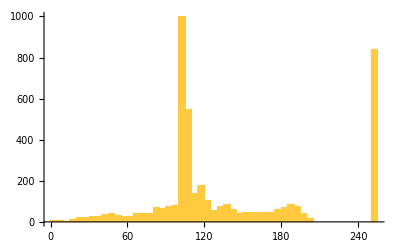
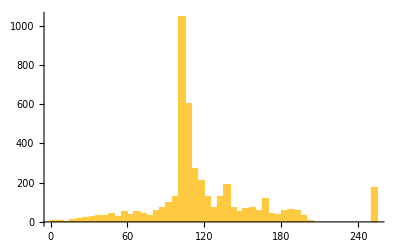
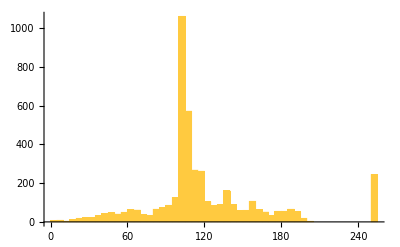
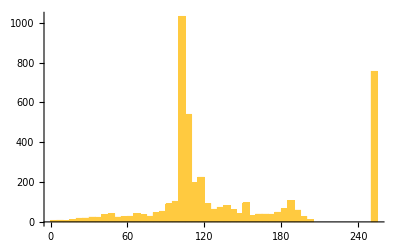
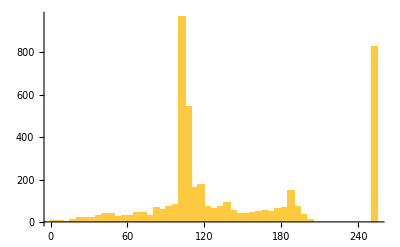
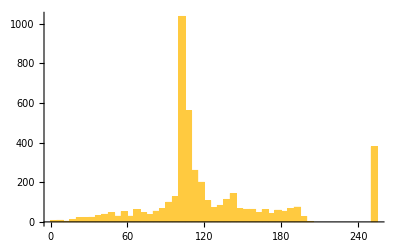
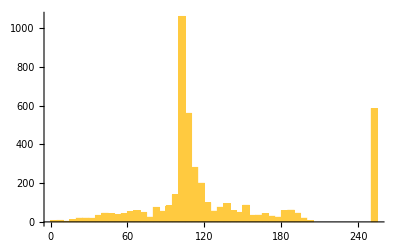
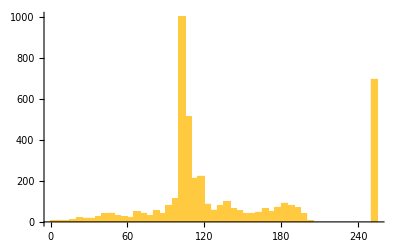

```mathematica
ParallelMap[Histogram[Module[{ru = #,ca,pcas},
ca = getca[ru];
pcas = Flatten[PerturbAll[{ca, ru}, #]&/@ Flatten[bodyidxs[ca], 1], 1];
TestCALifeTime/@ pcas]/.-Infinity->250, 50, PlotRange->All]&,quickneutral[{299459058088077823758143088095350287424,4,1}]]
```

```mathematica
Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

-Graphics-

```mathematica
CloseKernels[];
```

```mathematica
LaunchKernels[];
```

```mathematica
ParallelEvaluate[$MachineName]//Counts
```

<|theta→20,epsilon→24,delta→24,tremac→20,macstudio-basement→20,threadripper→32,threadripper2→64|>

## Picking Disease Examples

```mathematica
lts = Block[{ru = {299459058088077823758143088095350287424,4,1}},
ca = getca[ru];
pcas = Flatten[PerturbAll[{ca, ru}, #]&/@ Flatten[bodyidxs[ca], 1], 1];
TestCALifeTime/@ pcas];
```

```mathematica
Length[pcas]
```

4383

```mathematica
TestLifetime[{299459058088077823758143088095350287424,4,1},200]
```

101

```mathematica
Select[lts,#>0&&#<101&->"Index"]
```

{2,3,4,6,7,8,9,10,11,14,15,17,19,20,21,22,23,25,26,27,29,30,31,32,33,34,36,37,38,40,41,42,43,46,47,49,51,52,53,54,56,57,58,60,62,64,65,67,68,71,74,75,76,78,79,80,81,82,83,85,86,87,88,90,91,92,93,94,95,96,98,100,101,102,103,104,107,109,110,111,113,114,115,116,117,118,119,120,121,122,124,126,127,128,130,131,132,133,134,135,138,139,140,141,142,143,144,146,147,148,149,150,151,152,153,154,155,157,158,159,160,161,162,163,167,168,169,170,171,173,174,176,177,178,180,181,182,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,201,204,205,208,210,213,214,215,216,218,219,220,221,222,223,224,225,231,232,234,235,236,237,238,241,242,244,245,246,247,248,249,251,253,254,255,256,257,261,262,263,265,266,267,269,270,271,272,273,274,276,278,281,283,284,286,287,292,296,300,301,302,303,304,305,306,308,309,311,312,313,316,318,319,321,322,325,326,327,329,331,332,333,334,335,336,338,340,342,343,345,346,348,349,352,353,354,355,356,357,358,361,362,363,366,367,369,370,371,372,373,374,375,376,377,378,379,381,382,384,385,386,389,393,394,396,400,401,403,404,405,406,409,411,412,413,414,415,417,419,420,423,426,427,430,433,434,435,440,441,442,443,444,445,446,447,450,452,457,458,459,460,462,463,464,465,468,469,470,472,474,475,477,478,479,480,481,482,483,486,487,489,492,493,494,499,500,501,503,504,506,508,509,510,511,512,513,514,515,516,520,521,522,523,524,525,526,527,528,531,532,533,534,536,537,541,544,547,548,550,551,553,555,556,557,558,560,561,562,563,564,565,566,568,569,571,573,576,577,579,580,581,582,583,584,585,587,588,589,590,591,592,593,594,595,596,597,598,599,600,602,604,606,607,609,610,611,612,613,615,617,618,619,621,623,624,625,627,629,631,633,636,637,638,639,641,643,644,646,647,648,649,650,651,652,653,654,657,658,659,660,662,663,666,667,668,670,671,673,675,676,678,679,680,681,682,683,688,689,690,696,698,700,705,708,713,714,716,717,718,720,721,723,728,729,730,732,734,738,740,743,746,748,750,751,753,754,760,761,762,764,765,766,775,776,779,780,783,784,786,789,790,793,795,796,797,798,799,803,805,806,811,812,813,816,819,820,821,822,823,825,826,829,830,835,836,837,840,844,845,850,852,853,855,857,858,859,860,864,865,866,869,870,871,872,873,875,876,877,879,880,881,884,886,887,888,889,890,893,894,896,900,902,908,911,912,913,914,916,917,920,921,925,927,928,929,931,936,937,953,956,957,958,959,960,961,962,969,970,974,975,978,979,981,984,992,995,1000,1002,1004,1006,1007,1009,1011,1015,1016,1018,1019,1020,1023,1024,1028,1029,1034,1037,1039,1042,1044,1046,1047,1049,1050,1051,1052,1054,1057,1059,1060,1061,1062,1065,1070,1072,1075,1078,1080,1081,1084,1086,1087,1089,1090,1092,1098,1100,1105,1110,1111,1112,1113,1115,1116,1118,1119,1121,1129,1132,1134,1135,1137,1138,1139,1141,1146,1147,1150,1155,1163,1167,1168,1169,1170,1172,1176,1179,1184,1191,1192,1195,1197,1204,1205,1209,1211,1213,1214,1215,1219,1223,1227,1229,1230,1231,1234,1235,1249,1250,1251,1254,1257,1263,1265,1266,1271,1272,1273,1284,1285,1287,1290,1291,1292,1293,1294,1296,1299,1303,1306,1308,1309,1310,1315,1316,1317,1321,1323,1330,1331,1340,1343,1348,1349,1351,1354,1357,1360,1361,1362,1366,1367,1368,1376,1384,1387,1388,1389,1390,1391,1395,1401,1406,1408,1410,1417,1433,1439,1443,1446,1447,1453,1454,1477,1488,1489,1498,1508,1526,1529,1531,1532,1537,1542,1543,1561,1565,1577,1585,1587,1588,1589,1590,1593,1597,1633,1640,1641,1651,1655,1656,1662,1666,1668,1697,1703,1708,1713,1715,1716,1717,1721,1722,1723,1728,1730,1731,1767,1771,1774,1780,1784,1786,1790,1791,1793,1821,1825,1828,1833,1834,1840,1841,1844,1846,1851,1853,1873,1886,1887,1890,1894,1895,1901,1908,1910,1911,1913,1942,1943,1952,1965,1969,1970,1978,2008,2009,2014,2029,2035,2073,2080,2084,2093,2098,2101,2153,2160,2164,2167,2170,2226,2230,2233,2236,2239,2265,2278,2286,2296,2299,2302,2305,2308,2311,2346,2355,2362,2368,2370,2371,2374,2377,2380,2383,2386,2397,2412,2421,2430,2441,2442,2443,2446,2449,2452,2455,2458,2461,2493,2497,2518,2521,2524,2527,2530,2533,2536,2539,2576,2596,2599,2602,2605,2608,2611,2614,2617,2620,2631,2640,2653,2656,2660,2666,2671,2672,2674,2677,2680,2683,2686,2689,2692,2695,2698,2701,2721,2731,2735,2736,2740,2747,2755,2758,2761,2764,2767,2770,2773,2776,2779,2782,2785,2811,2812,2815,2818,2839,2842,2845,2848,2851,2854,2857,2860,2863,2866,2869,2872,2883,2899,2901,2913,2920,2923,2926,2929,2932,2935,2938,2941,2944,2947,2950,2953,2956,2981,2983,2998,3001,3004,3007,3010,3013,3016,3019,3022,3025,3028,3031,3034,3037,3058,3061,3073,3076,3079,3082,3085,3088,3091,3094,3097,3100,3103,3106,3109,3112,3115,3126,3139,3142,3145,3148,3151,3154,3157,3160,3163,3166,3169,3172,3175,3178,3181,3184,3187,3211,3214,3217,3220,3223,3226,3229,3232,3235,3238,3241,3244,3247,3250,3253,3256,3259,3270,3283,3286,3289,3292,3295,3298,3301,3304,3307,3310,3313,3316,3319,3322,3325,3328,3331,3334,3345,3358,3361,3364,3367,3370,3373,3376,3379,3382,3385,3388,3391,3394,3397,3400,3403,3406,3409,3412,3433,3436,3439,3442,3445,3448,3451,3454,3457,3460,3463,3466,3469,3472,3475,3478,3481,3484,3487,3511,3514,3517,3520,3523,3526,3529,3532,3535,3538,3541,3544,3547,3550,3553,3556,3559,3562,3565,3592,3595,3598,3601,3604,3607,3610,3613,3616,3619,3622,3625,3628,3631,3634,3637,3640,3643,3670,3673,3676,3679,3682,3685,3688,3691,3694,3697,3700,3703,3706,3709,3712,3715,3718,3748,3751,3754,3757,3760,3763,3766,3769,3772,3775,3778,3781,3784,3787,3790,3793,3829,3832,3835,3838,3841,3844,3847,3850,3853,3856,3859,3862,3865,3868,3871,3913,3916,3919,3922,3925,3928,3931,3934,3937,3940,3943,3946,3949,3952,3994,3997,4000,4003,4006,4009,4012,4015,4018,4021,4024,4027,4030,4072,4075,4078,4081,4084,4087,4090,4093,4096,4099,4102,4105,4147,4150,4153,4156,4159,4162,4165,4168,4171,4174,4177,4219,4222,4225,4228,4231,4234,4237,4240,4243,4246,4249,4252,4255,4258,4261,4264,4267,4270,4273,4276,4279,4282,4285,4288,4291,4294,4297,4300,4303,4306,4309,4312,4315,4318,4321,4324,4327,4330,4333,4336,4339,4342,4345,4348,4351,4354,4357,4360,4363,4366,4369,4372,4375,4378,4381}

```mathematica
Length[%]
```

1314

```mathematica
allperts[{299459058088077823758143088095350287424,4,1}]
```

```mathematica
[[]]
```

```mathematica
Select[Flatten[],15<First[Keys[#]][[1]]<80&]
```

{<|{16,198}→0|>,<|{16,198}→3|>,<|{16,199}→3|>,<|{16,200}→0|>,<|{16,200}→2|>,<|{16,200}→3|>,<|{16,201}→2|>,<|{16,201}→3|>,<|{16,202}→1|>,<|{16,202}→2|>,<|{16,202}→3|>,<|{16,203}→0|>,<|{16,203}→2|>,<|{16,203}→3|>,<|{16,205}→3|>,<|{16,206}→0|>,<|{16,206}→3|>,<|{17,198}→0|>,<|{17,198}→1|>,<|{17,198}→3|>,<|{17,199}→0|>,<|{17,200}→0|>,<|{17,200}→1|>,<|{17,201}→0|>,<|{17,201}→1|>,<|{17,201}→2|>,<|{17,202}→0|>,<|{17,202}→2|>,<|{17,202}→3|>,<|{17,203}→1|>,<|{17,204}→0|>,<|{17,204}→2|>,<|{17,204}→3|>,<|{17,205}→0|>,<|{17,205}→1|>,<|{17,206}→3|>,<|{18,198}→0|>,<|{18,198}→1|>,<|{18,199}→0|>,<|{18,199}→1|>,<|{18,199}→3|>,<|{18,200}→2|>,<|{18,200}→3|>,<|{18,201}→0|>,<|{18,201}→1|>,<|{18,201}→2|>,<|{18,202}→0|>,<|{18,202}→2|>,<|{18,203}→2|>,<|{18,204}→1|>,<|{18,205}→0|>,<|{18,205}→2|>,<|{18,206}→0|>,<|{18,206}→2|>,<|{19,198}→0|>,<|{19,199}→1|>,<|{19,200}→2|>,<|{19,201}→0|>,<|{19,201}→2|>,<|{19,201}→3|>,<|{19,202}→1|>,<|{19,202}→2|>,<|{19,202}→3|>,<|{19,203}→1|>,<|{19,203}→2|>,<|{19,204}→2|>,<|{19,204}→3|>,<|{19,205}→0|>,<|{19,206}→0|>,<|{19,206}→3|>,<|{19,207}→1|>,<|{19,207}→3|>,<|{19,208}→0|>,<|{20,198}→0|>,<|{20,198}→1|>,<|{20,198}→3|>,<|{20,199}→2|>,<|{20,200}→0|>,<|{20,200}→1|>,<|{20,200}→2|>,<|{20,201}→0|>,<|{20,201}→1|>,<|{20,201}→2|>,<|{20,202}→2|>,<|{20,203}→0|>,<|{20,203}→3|>,<|{20,204}→0|>,<|{20,204}→2|>,<|{20,205}→0|>,<|{20,205}→3|>,<|{20,206}→1|>,<|{20,207}→0|>,<|{20,207}→1|>,<|{20,207}→3|>,<|{21,198}→0|>,<|{21,198}→1|>,<|{21,198}→3|>,<|{21,199}→0|>,<|{21,200}→0|>,<|{21,200}→2|>,<|{21,200}→3|>,<|{21,201}→3|>,<|{21,202}→0|>,<|{21,202}→2|>,<|{21,203}→0|>,<|{21,203}→2|>,<|{21,203}→3|>,<|{21,204}→0|>,<|{21,204}→1|>,<|{21,204}→2|>,<|{21,205}→0|>,<|{21,205}→1|>,<|{21,205}→2|>,<|{22,198}→0|>,<|{22,198}→3|>,<|{22,199}→0|>,<|{22,199}→2|>,<|{22,200}→0|>,<|{22,200}→2|>,<|{22,201}→1|>,<|{22,202}→3|>,<|{22,203}→0|>,<|{22,203}→3|>,<|{22,205}→0|>,<|{22,205}→2|>,<|{22,206}→0|>,<|{22,206}→1|>,<|{22,206}→3|>,<|{23,198}→0|>,<|{23,199}→0|>,<|{23,199}→3|>,<|{23,200}→0|>,<|{23,200}→1|>,<|{23,200}→2|>,<|{23,201}→0|>,<|{23,201}→3|>,<|{23,202}→1|>,<|{23,202}→3|>,<|{23,203}→3|>,<|{23,204}→3|>,<|{23,205}→0|>,<|{23,206}→0|>,<|{24,197}→0|>,<|{24,197}→2|>,<|{24,197}→3|>,<|{24,199}→1|>,<|{24,199}→3|>,<|{24,200}→0|>,<|{24,200}→2|>,<|{24,200}→3|>,<|{24,201}→0|>,<|{24,201}→1|>,<|{24,201}→2|>,<|{24,202}→3|>,<|{24,203}→1|>,<|{24,205}→0|>,<|{24,205}→1|>,<|{24,205}→3|>,<|{24,206}→0|>,<|{24,206}→2|>,<|{24,207}→0|>,<|{24,207}→1|>,<|{24,207}→2|>,<|{25,197}→3|>,<|{25,198}→0|>,<|{25,198}→2|>,<|{25,199}→0|>,<|{25,199}→3|>,<|{25,200}→0|>,<|{25,200}→2|>,<|{25,201}→0|>,<|{25,201}→2|>,<|{25,201}→3|>,<|{25,202}→0|>,<|{25,202}→1|>,<|{25,202}→2|>,<|{25,203}→3|>,<|{25,204}→0|>,<|{25,204}→3|>,<|{25,205}→3|>,<|{25,206}→1|>,<|{25,206}→2|>,<|{25,208}→0|>,<|{25,208}→1|>,<|{25,208}→3|>,<|{26,197}→1|>,<|{26,197}→3|>,<|{26,198}→1|>,<|{26,199}→1|>,<|{26,199}→2|>,<|{26,199}→3|>,<|{26,200}→0|>,<|{26,200}→1|>,<|{26,200}→2|>,<|{26,201}→0|>,<|{26,201}→1|>,<|{26,201}→3|>,<|{26,203}→0|>,<|{26,203}→1|>,<|{26,203}→2|>,<|{26,204}→0|>,<|{26,204}→2|>,<|{26,204}→3|>,<|{26,205}→1|>,<|{26,205}→2|>,<|{26,205}→3|>,<|{26,206}→3|>,<|{26,207}→0|>,<|{26,207}→1|>,<|{26,207}→3|>,<|{26,208}→2|>,<|{26,208}→3|>,<|{27,198}→1|>,<|{27,199}→1|>,<|{27,200}→0|>,<|{27,200}→2|>,<|{27,201}→0|>,<|{27,201}→1|>,<|{27,202}→0|>,<|{27,202}→2|>,<|{27,203}→0|>,<|{27,203}→2|>,<|{27,203}→3|>,<|{27,204}→1|>,<|{27,204}→2|>,<|{27,205}→0|>,<|{27,205}→1|>,<|{27,205}→2|>,<|{27,206}→1|>,<|{27,206}→2|>,<|{27,207}→0|>,<|{27,207}→1|>,<|{27,208}→0|>,<|{27,208}→3|>,<|{27,209}→2|>,<|{28,200}→0|>,<|{28,200}→3|>,<|{28,201}→1|>,<|{28,201}→2|>,<|{28,201}→3|>,<|{28,202}→0|>,<|{28,202}→1|>,<|{28,202}→2|>,<|{28,203}→1|>,<|{28,203}→3|>,<|{28,204}→0|>,<|{28,204}→2|>,<|{28,204}→3|>,<|{28,205}→0|>,<|{28,205}→2|>,<|{28,205}→3|>,<|{28,206}→0|>,<|{28,206}→1|>,<|{28,206}→2|>,<|{28,207}→0|>,<|{28,207}→1|>,<|{28,207}→3|>,<|{28,208}→1|>,<|{28,209}→1|>,<|{28,209}→3|>,<|{28,210}→0|>,<|{28,210}→3|>,<|{29,202}→0|>,<|{29,202}→2|>,<|{29,202}→3|>,<|{29,203}→0|>,<|{29,203}→3|>,<|{29,204}→1|>,<|{29,204}→3|>,<|{29,205}→0|>,<|{29,205}→3|>,<|{29,206}→1|>,<|{29,206}→2|>,<|{29,207}→0|>,<|{29,207}→3|>,<|{29,208}→2|>,<|{29,209}→0|>,<|{29,209}→2|>,<|{30,202}→3|>,<|{30,203}→0|>,<|{30,203}→2|>,<|{30,203}→3|>,<|{30,204}→1|>,<|{30,205}→0|>,<|{30,205}→2|>,<|{30,206}→0|>,<|{30,206}→1|>,<|{30,206}→2|>,<|{30,207}→0|>,<|{30,207}→2|>,<|{30,207}→3|>,<|{30,208}→0|>,<|{30,208}→1|>,<|{30,208}→3|>,<|{30,209}→3|>,<|{30,210}→0|>,<|{30,210}→1|>,<|{30,210}→3|>,<|{31,202}→1|>,<|{31,202}→3|>,<|{31,203}→3|>,<|{31,204}→0|>,<|{31,204}→2|>,<|{31,205}→0|>,<|{31,205}→1|>,<|{31,206}→0|>,<|{31,206}→3|>,<|{31,207}→0|>,<|{31,207}→2|>,<|{31,208}→0|>,<|{31,208}→2|>,<|{31,208}→3|>,<|{31,209}→0|>,<|{31,209}→1|>,<|{32,203}→0|>,<|{32,203}→1|>,<|{32,203}→3|>,<|{32,205}→3|>,<|{32,206}→1|>,<|{32,207}→0|>,<|{32,208}→2|>,<|{32,209}→3|>,<|{33,203}→2|>,<|{33,203}→3|>,<|{33,204}→1|>,<|{33,204}→2|>,<|{33,205}→0|>,<|{33,205}→2|>,<|{33,206}→0|>,<|{33,206}→3|>,<|{33,208}→2|>,<|{33,208}→3|>,<|{33,209}→0|>,<|{33,209}→2|>,<|{33,210}→1|>,<|{34,202}→3|>,<|{34,203}→1|>,<|{34,204}→2|>,<|{34,205}→2|>,<|{34,206}→0|>,<|{34,206}→3|>,<|{34,207}→0|>,<|{34,207}→3|>,<|{34,208}→0|>,<|{34,210}→0|>,<|{34,210}→2|>,<|{34,210}→3|>,<|{34,211}→1|>,<|{34,211}→3|>,<|{35,202}→0|>,<|{35,205}→1|>,<|{35,205}→2|>,<|{35,206}→1|>,<|{35,206}→3|>,<|{35,207}→3|>,<|{35,208}→0|>,<|{35,208}→3|>,<|{35,209}→3|>,<|{35,210}→0|>,<|{35,211}→0|>,<|{35,211}→3|>,<|{36,202}→0|>,<|{36,202}→1|>,<|{36,202}→2|>,<|{36,203}→0|>,<|{36,204}→2|>,<|{36,205}→0|>,<|{36,205}→1|>,<|{36,207}→0|>,<|{36,207}→1|>,<|{36,207}→3|>,<|{36,208}→3|>,<|{36,209}→3|>,<|{36,210}→0|>,<|{36,210}→1|>,<|{36,210}→3|>,<|{36,211}→0|>,<|{36,211}→2|>,<|{36,212}→0|>,<|{37,201}→0|>,<|{37,201}→2|>,<|{37,203}→0|>,<|{37,203}→2|>,<|{37,203}→3|>,<|{37,204}→3|>,<|{37,206}→1|>,<|{37,206}→2|>,<|{37,208}→0|>,<|{37,208}→3|>,<|{37,209}→0|>,<|{37,209}→3|>,<|{37,210}→2|>,<|{37,210}→3|>,<|{37,211}→1|>,<|{37,211}→2|>,<|{37,212}→3|>,<|{37,213}→0|>,<|{37,213}→1|>,<|{38,201}→1|>,<|{38,201}→3|>,<|{38,202}→0|>,<|{38,202}→2|>,<|{38,202}→3|>,<|{38,203}→1|>,<|{38,203}→3|>,<|{38,204}→1|>,<|{38,204}→3|>,<|{38,205}→0|>,<|{38,205}→2|>,<|{38,206}→1|>,<|{38,207}→0|>,<|{38,207}→1|>,<|{38,207}→3|>,<|{38,208}→0|>,<|{38,208}→1|>,<|{38,209}→2|>,<|{38,209}→3|>,<|{38,210}→2|>,<|{38,211}→3|>,<|{38,212}→1|>,<|{39,201}→1|>,<|{39,202}→1|>,<|{39,202}→3|>,<|{39,203}→0|>,<|{39,203}→2|>,<|{39,204}→0|>,<|{39,204}→1|>,<|{39,205}→1|>,<|{39,205}→2|>,<|{39,207}→1|>,<|{39,207}→3|>,<|{39,208}→1|>,<|{39,208}→2|>,<|{39,209}→1|>,<|{39,210}→3|>,<|{39,211}→1|>,<|{40,202}→1|>,<|{40,203}→1|>,<|{40,203}→3|>,<|{40,204}→1|>,<|{40,204}→2|>,<|{40,204}→3|>,<|{40,205}→1|>,<|{40,205}→2|>,<|{40,207}→3|>,<|{40,208}→1|>,<|{40,209}→2|>,<|{40,209}→3|>,<|{40,210}→3|>,<|{40,211}→1|>,<|{40,211}→3|>,<|{40,212}→3|>,<|{40,215}→1|>,<|{41,201}→1|>,<|{41,203}→1|>,<|{41,203}→3|>,<|{41,204}→2|>,<|{41,205}→1|>,<|{41,205}→2|>,<|{41,206}→0|>,<|{41,206}→3|>,<|{41,208}→1|>,<|{41,208}→2|>,<|{41,209}→1|>,<|{41,209}→2|>,<|{41,209}→3|>,<|{41,210}→3|>,<|{41,211}→1|>,<|{41,212}→2|>,<|{41,212}→3|>,<|{41,214}→1|>,<|{42,201}→1|>,<|{42,202}→1|>,<|{42,203}→1|>,<|{42,203}→3|>,<|{42,204}→2|>,<|{42,204}→3|>,<|{42,205}→2|>,<|{42,205}→3|>,<|{42,206}→0|>,<|{42,206}→1|>,<|{42,207}→0|>,<|{42,208}→0|>,<|{42,208}→2|>,<|{42,209}→1|>,<|{42,209}→2|>,<|{42,209}→3|>,<|{42,210}→3|>,<|{42,212}→1|>,<|{42,213}→0|>,<|{42,214}→1|>,<|{42,215}→0|>,<|{42,215}→3|>,<|{43,206}→0|>,<|{43,207}→0|>,<|{43,207}→2|>,<|{43,208}→1|>,<|{43,208}→3|>,<|{43,209}→0|>,<|{43,209}→3|>,<|{43,211}→3|>,<|{43,212}→2|>,<|{43,214}→0|>,<|{44,206}→3|>,<|{44,207}→0|>,<|{44,207}→2|>,<|{44,207}→3|>,<|{44,208}→1|>,<|{44,208}→2|>,<|{44,209}→2|>,<|{44,209}→3|>,<|{44,210}→1|>,<|{44,213}→0|>,<|{44,214}→0|>,<|{44,214}→3|>,<|{45,206}→0|>,<|{45,206}→2|>,<|{45,207}→0|>,<|{45,207}→1|>,<|{45,208}→1|>,<|{45,209}→2|>,<|{45,210}→0|>,<|{45,211}→0|>,<|{45,212}→3|>,<|{45,215}→1|>,<|{46,205}→3|>,<|{46,206}→0|>,<|{46,206}→2|>,<|{46,206}→3|>,<|{46,207}→2|>,<|{46,208}→3|>,<|{46,209}→3|>,<|{46,211}→1|>,<|{46,213}→3|>,<|{46,214}→1|>,<|{46,215}→0|>,<|{46,215}→3|>,<|{47,206}→0|>,<|{47,206}→1|>,<|{47,207}→2|>,<|{47,208}→2|>,<|{47,209}→0|>,<|{47,209}→1|>,<|{47,209}→3|>,<|{47,211}→0|>,<|{47,212}→1|>,<|{47,213}→3|>,<|{47,214}→2|>,<|{47,214}→3|>,<|{47,215}→0|>,<|{47,216}→0|>,<|{47,216}→2|>,<|{48,208}→0|>,<|{48,208}→1|>,<|{48,208}→2|>,<|{48,209}→3|>,<|{48,210}→3|>,<|{48,212}→3|>,<|{48,213}→1|>,<|{48,213}→3|>,<|{48,215}→2|>,<|{48,215}→3|>,<|{48,216}→0|>,<|{49,205}→3|>,<|{49,206}→0|>,<|{49,206}→3|>,<|{49,207}→3|>,<|{49,208}→0|>,<|{49,208}→1|>,<|{49,208}→2|>,<|{49,209}→1|>,<|{49,209}→3|>,<|{49,210}→3|>,<|{49,212}→0|>,<|{49,213}→0|>,<|{49,213}→3|>,<|{49,214}→0|>,<|{49,214}→1|>,<|{49,216}→0|>,<|{49,216}→1|>,<|{49,216}→3|>,<|{49,218}→0|>,<|{49,218}→3|>,<|{50,205}→1|>,<|{50,205}→2|>,<|{50,208}→2|>,<|{50,209}→1|>,<|{50,211}→0|>,<|{50,211}→1|>,<|{50,212}→0|>,<|{50,213}→0|>,<|{50,214}→0|>,<|{50,215}→0|>,<|{50,215}→1|>,<|{50,215}→3|>,<|{50,217}→0|>,<|{50,217}→1|>,<|{50,217}→3|>,<|{51,205}→2|>,<|{51,208}→0|>,<|{51,209}→0|>,<|{51,209}→1|>,<|{51,209}→2|>,<|{51,210}→1|>,<|{51,210}→2|>,<|{51,211}→3|>,<|{51,213}→3|>,<|{51,215}→2|>,<|{51,216}→0|>,<|{51,216}→3|>,<|{52,204}→0|>,<|{52,209}→2|>,<|{52,211}→1|>,<|{52,212}→3|>,<|{52,213}→3|>,<|{52,214}→0|>,<|{52,216}→0|>,<|{52,216}→2|>,<|{53,209}→0|>,<|{53,212}→3|>,<|{53,213}→0|>,<|{53,216}→0|>,<|{54,202}→2|>,<|{54,208}→1|>,<|{54,209}→2|>,<|{54,210}→0|>,<|{54,210}→2|>,<|{54,212}→0|>,<|{54,213}→3|>,<|{54,214}→0|>,<|{55,202}→0|>,<|{55,203}→2|>,<|{55,207}→2|>,<|{55,210}→0|>,<|{55,210}→3|>,<|{55,211}→0|>,<|{55,211}→1|>,<|{55,211}→2|>,<|{55,212}→3|>,<|{55,214}→0|>,<|{56,207}→0|>,<|{56,209}→1|>,<|{56,209}→3|>,<|{56,213}→0|>,<|{56,214}→1|>,<|{56,214}→3|>,<|{56,216}→3|>,<|{56,218}→0|>,<|{56,218}→3|>,<|{57,208}→2|>,<|{57,210}→1|>,<|{57,212}→0|>,<|{57,213}→3|>,<|{57,214}→1|>,<|{57,214}→3|>,<|{57,215}→0|>,<|{57,216}→1|>,<|{57,216}→3|>,<|{57,217}→0|>,<|{57,218}→3|>,<|{57,219}→2|>,<|{57,219}→3|>,<|{58,209}→3|>,<|{58,211}→0|>,<|{58,212}→0|>,<|{58,214}→0|>,<|{58,215}→1|>,<|{58,216}→0|>,<|{58,217}→1|>,<|{58,217}→3|>,<|{58,218}→2|>,<|{59,206}→3|>,<|{59,208}→0|>,<|{59,209}→1|>,<|{59,210}→3|>,<|{59,211}→0|>,<|{59,213}→0|>,<|{59,213}→1|>,<|{59,214}→2|>,<|{59,215}→0|>,<|{59,216}→3|>,<|{59,217}→2|>,<|{60,203}→0|>,<|{60,207}→2|>,<|{60,207}→3|>,<|{60,208}→3|>,<|{60,210}→0|>,<|{60,210}→1|>,<|{60,212}→2|>,<|{60,214}→2|>,<|{60,215}→1|>,<|{60,215}→3|>,<|{60,216}→2|>,<|{61,206}→0|>,<|{61,206}→2|>,<|{61,209}→1|>,<|{61,213}→3|>,<|{61,215}→0|>,<|{61,215}→2|>,<|{62,198}→0|>,<|{62,208}→0|>,<|{62,208}→2|>,<|{62,210}→0|>,<|{62,215}→0|>,<|{63,197}→0|>,<|{63,209}→3|>,<|{63,212}→0|>,<|{63,213}→1|>,<|{63,216}→1|>,<|{64,197}→0|>,<|{64,198}→0|>,<|{64,215}→2|>,<|{64,217}→3|>,<|{65,197}→0|>,<|{65,198}→0|>,<|{65,199}→0|>,<|{65,217}→3|>,<|{66,197}→0|>,<|{66,198}→0|>,<|{66,199}→0|>,<|{66,200}→0|>,<|{66,208}→3|>,<|{66,213}→0|>,<|{66,215}→3|>,<|{66,219}→0|>,<|{67,197}→0|>,<|{67,198}→0|>,<|{67,199}→0|>,<|{67,200}→0|>,<|{67,201}→0|>,<|{67,212}→3|>,<|{67,215}→3|>,<|{67,218}→0|>,<|{67,220}→0|>,<|{67,220}→3|>,<|{68,197}→0|>,<|{68,198}→0|>,<|{68,199}→0|>,<|{68,200}→0|>,<|{68,201}→0|>,<|{68,202}→0|>,<|{68,205}→3|>,<|{68,210}→3|>,<|{68,213}→3|>,<|{68,216}→3|>,<|{68,220}→2|>,<|{68,220}→3|>,<|{69,197}→0|>,<|{69,198}→0|>,<|{69,199}→0|>,<|{69,200}→0|>,<|{69,201}→0|>,<|{69,202}→0|>,<|{69,203}→0|>,<|{69,213}→3|>,<|{69,215}→0|>,<|{70,197}→0|>,<|{70,198}→0|>,<|{70,199}→0|>,<|{70,200}→0|>,<|{70,201}→0|>,<|{70,202}→0|>,<|{70,203}→0|>,<|{70,204}→0|>,<|{70,216}→2|>,<|{71,197}→0|>,<|{71,198}→0|>,<|{71,199}→0|>,<|{71,200}→0|>,<|{71,201}→0|>,<|{71,202}→0|>,<|{71,203}→0|>,<|{71,204}→0|>,<|{71,205}→0|>,<|{71,208}→3|>,<|{71,211}→3|>,<|{71,216}→0|>,<|{71,217}→0|>,<|{71,218}→1|>,<|{71,220}→2|>,<|{71,222}→0|>,<|{71,222}→2|>,<|{72,197}→0|>,<|{72,198}→0|>,<|{72,199}→0|>,<|{72,200}→0|>,<|{72,201}→0|>,<|{72,202}→0|>,<|{72,203}→0|>,<|{72,204}→0|>,<|{72,205}→0|>,<|{72,206}→0|>,<|{72,212}→3|>,<|{72,216}→0|>,<|{72,217}→2|>,<|{72,217}→3|>,<|{72,219}→0|>,<|{72,221}→2|>,<|{73,197}→0|>,<|{73,198}→0|>,<|{73,199}→0|>,<|{73,200}→0|>,<|{73,201}→0|>,<|{73,202}→0|>,<|{73,203}→0|>,<|{73,204}→0|>,<|{73,205}→0|>,<|{73,206}→0|>,<|{73,207}→0|>,<|{73,215}→3|>,<|{73,216}→0|>,<|{73,217}→0|>,<|{73,218}→0|>,<|{74,197}→0|>,<|{74,198}→0|>,<|{74,199}→0|>,<|{74,200}→0|>,<|{74,201}→0|>,<|{74,202}→0|>,<|{74,203}→0|>,<|{74,204}→0|>,<|{74,205}→0|>,<|{74,206}→0|>,<|{74,207}→0|>,<|{74,208}→0|>,<|{74,211}→3|>,<|{74,217}→0|>,<|{74,217}→2|>,<|{74,221}→3|>,<|{75,197}→0|>,<|{75,198}→0|>,<|{75,199}→0|>,<|{75,200}→0|>,<|{75,201}→0|>,<|{75,202}→0|>,<|{75,203}→0|>,<|{75,204}→0|>,<|{75,205}→0|>,<|{75,206}→0|>,<|{75,207}→0|>,<|{75,208}→0|>,<|{75,209}→0|>,<|{75,217}→2|>,<|{75,218}→0|>,<|{76,197}→0|>,<|{76,198}→0|>,<|{76,199}→0|>,<|{76,200}→0|>,<|{76,201}→0|>,<|{76,202}→0|>,<|{76,203}→0|>,<|{76,204}→0|>,<|{76,205}→0|>,<|{76,206}→0|>,<|{76,207}→0|>,<|{76,208}→0|>,<|{76,209}→0|>,<|{76,210}→0|>,<|{76,217}→0|>,<|{76,218}→0|>,<|{77,197}→0|>,<|{77,198}→0|>,<|{77,199}→0|>,<|{77,200}→0|>,<|{77,201}→0|>,<|{77,202}→0|>,<|{77,203}→0|>,<|{77,204}→0|>,<|{77,205}→0|>,<|{77,206}→0|>,<|{77,207}→0|>,<|{77,208}→0|>,<|{77,209}→0|>,<|{77,210}→0|>,<|{77,211}→0|>,<|{77,214}→3|>,<|{77,219}→0|>,<|{78,197}→0|>,<|{78,198}→0|>,<|{78,199}→0|>,<|{78,200}→0|>,<|{78,201}→0|>,<|{78,202}→0|>,<|{78,203}→0|>,<|{78,204}→0|>,<|{78,205}→0|>,<|{78,206}→0|>,<|{78,207}→0|>,<|{78,208}→0|>,<|{78,209}→0|>,<|{78,210}→0|>,<|{78,211}→0|>,<|{78,212}→0|>,<|{79,197}→0|>,<|{79,198}→0|>,<|{79,199}→0|>,<|{79,200}→0|>,<|{79,201}→0|>,<|{79,202}→0|>,<|{79,203}→0|>,<|{79,204}→0|>,<|{79,205}→0|>,<|{79,206}→0|>,<|{79,207}→0|>,<|{79,208}→0|>,<|{79,209}→0|>,<|{79,210}→0|>,<|{79,211}→0|>,<|{79,212}→0|>,<|{79,213}→0|>,<|{79,216}→3|>}

```mathematica
Length[%]
```

911

```mathematica
RandomSample[,20]
```

{<|{50,217}→1|>,<|{22,202}→3|>,<|{31,207}→0|>,<|{56,207}→0|>,<|{79,209}→0|>,<|{22,198}→0|>,<|{73,215}→3|>,<|{36,207}→3|>,<|{75,209}→0|>,<|{48,215}→2|>,<|{35,206}→3|>,<|{37,211}→2|>,<|{51,210}→2|>,<|{31,203}→3|>,<|{70,199}→0|>,<|{77,208}→0|>,<|{43,214}→0|>,<|{22,203}→0|>,<|{71,201}→0|>,<|{20,199}→2|>}

```mathematica
PlotCA[{PerturbCA[{299459058088077823758143088095350287424,4,1},#],#}]&/@
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{{1},0}
```

```mathematica
PerturbedCellularAutomaton[rule,init,t,<|{XXX}->XX,{XXX}->XX|>]
```

```mathematica
PlotCA[]
```

```mathematica
ResourceFunction["InteractiveListSelector"][PlotCA[{PerturbCA[{299459058088077823758143088095350287424,4,1},#][[;;120]],#}]->#&/@(RandomSample[#,20]&[Select[allperts[{299459058088077823758143088095350287424,4,1}][[Select[lts,#>0&&#<101&->"Index"]]],15<First[Keys[#]][[1]]<80&]])]
```

{<|{16,206}→0|>,<|{29,209}→2|>,<|{24,202}→3|>}

```mathematica
ResourceFunction["InteractiveListSelector"][PlotCA[{PerturbCA[{299459058088077823758143088095350287424,4,1},#][[;;120]],#}]->#&/@(RandomSample[#,20]&[Select[allperts[{299459058088077823758143088095350287424,4,1}][[Select[lts,#>0&&95<#<105&->"Index"]]],15<First[Keys[#]][[1]]<80&]])]
```

{<|{17,203}→0|>,<|{54,205}→0|>}

{<|{17,203}→0|>,<|{54,205}→0|>,<|{38,208}→3|>}

```mathematica
ResourceFunction["InteractiveListSelector"][PlotCA[{PerturbCA[{299459058088077823758143088095350287424,4,1},#][[;;120]],#}]->#&/@(RandomSample[#,20]&[Select[allperts[{299459058088077823758143088095350287424,4,1}][[Select[lts,#<0&->"Index"]]],15<First[Keys[#]][[1]]<80&]])]
```

{<|{35,209}→0|>,<|{33,207}→0|>}

```mathematica
PlotCA[PerturbCA[{299459058088077823758143088095350287424,4,1},#]]&/@{<|{35,209}->0|>,<|{33,207}->0|>}
```

{-Graphics-,-Graphics-}

```mathematica
ResourceFunction["InteractiveListSelector"][PlotCA[{PerturbCA[{299459058088077823758143088095350287424,4,1},#][[;;120]],#}]->#&/@{<|{16,206}->0|>,<|{29,209}->2|>,<|{24,202}->3|>,<|{17,203}->0|>,<|{54,205}->0|>,<|{38,208}->3|>,<|{33,207}->0|>}]
```

{<|{17,203}→0|>,<|{38,208}→3|>,<|{16,206}→0|>,<|{54,205}→0|>,<|{29,209}→2|>,<|{24,202}→3|>,<|{33,207}→0|>}

```mathematica
GraphicsRow[PlotCA[{PerturbCA[{299459058088077823758143088095350287424,4,1},#][[;;120]],#}]&/@{<|{17,203}->0|>,<|{38,208}->3|>,<|{16,206}->0|>,<|{54,205}->0|>,<|{29,209}->2|>,<|{24,202}->3|>,<|{33,207}->0|>}]
```

-Graphics-

### Therapy search

```mathematica
PerturbCA[{299459058088077823758143088095350287424,4,1},<|{16,206}->0|>]
```

```mathematica
HealCA[{299459058088077823758143088095350287424,4,1},<|{16,206}->0|>,All];
```

```mathematica
%296[[4]]
```

```mathematica
TestCALifeTime[First[#]]&/@
```

{42,42,136,42,50,46,41,37,95,30,37,31,25,32,29,68,82,55,85,85,58,46,85,99,111,149,85,42,115,33,42,42,49,50,48,122,37,55,22,51,45,65,132,81,176,44,68,97,85,85,85,51,61,97,85,85,42,79,61,79,115,72,50,37,42,31,143,61,39,85,30,52,32,131,176,91,59,85,53,72,97,60,136,95,91,41,85,85,85,42,50,43,79,77,35,44,33,131,126,143,37,29,149,58,82,39,85,145,131,176,85,85,97,58,91,45,85,44,149,42,43,56,37,37,85,92,46,32,76,70,173,85,55,43,116,45,39,85,95,90,35,85,40,88,77,41,50,42,81,57,48,80,39,35,85,71,96,85,50,43,130,74,88,47,147,85,151,124,130,53,47,152,73,70,57,43,57,122,47,41,43,60,48,85,85,35,52,74,78,128,49,85,51,96,85,44,69,152,90,64,60,85,130,130,138,46,187,45,45,41,43,193,51,60,83,129,58,78,67,85,49,46,67,85,38,53,97,85,85,53,44,69,50,142,130,153,130,80,130,60,91,43,70,61,51,55,145,34,60,85,47,85,40,46,45,85,128,47,47,43,85,58,63,85,66,107,67,66,123,69,57,142,44,130,47,63,130,88,46,40,186,105,85,38,141,85,131,85,85,151,85,43,138,55,85,65,61,63,85,85,125,175,66,79,61,60,79,177,44,45,78,43,53,89,130,85,85,136,43,60,44,85,38,34,131,85,45,85,65,67,43,44,85,85,54,109,85,85,110,66,58,85,45,54,139,46,85,130,85,130,45,43,61,36,38,130,67,131,85,85,45,61,109,41,85,55,85,55,85,79,85,44,45,178,48,46,116,45,85,130,45,85,55,38,85,50,109,85,44,85,85,50,85,43,79,110,85,112,44,45,55,48,46,39,139,85,45,41,85,43,50,52,41,85,46,46,67,49,65,85,62,65,110,43,144,110,85,69,44,45,38,61,46,85,55,85,139,51,43,133,49,92,85,85,69,132,110,50,119,110,43,68,64,85,85,43,45,170,46,85,57,85,45,54,46,85,42,150,85,71,110,65,68,110,85,68,110,43,85,158,64,85,44,45,85,136,85,47,107,85,67,85,85,85,116,110,162,126,110,65,85,110,85,53,85,62,55,55,55,85,64,46,85,89,85,87,107,105,103,95,75,85,85,193,100,110,85,142,110,162,85,64,65,85,119,50,85,51,85,57,85,68,83,64,152,103,65,102,85,85,66,173,85,181,110,102,85,110,85,68,162,122,160,147,69,49,49,96,85,89,85,86,85,123,67,85,85,97,173,60,88,85,158,85,85,58,64,110,85,107,110,111,147,111,85,79,162,105,85,79,85,74,103,81,63,105,87,85,71,85,192,122,97,57,85,85,58,108,64,76,85,165,66,85,122,176,110,104,110,85,86,111,85,114,102,108,85,66,94,85,85,120,93,104,87,81,55,71,85,85,71,56,85,54,67,95,58,85,85,81,107,85,55,154,110,96,152,81,120,105,85,85,85,68,119,85,123,89,72,104,85,84,147,61,81,85,85,70,61,59,85,66,85,85,91,140,127,55,85,85,116,85,85,85,110,85,112,96,85,179,70,142,85,85,99,59,84,85,168,72,72,102,81,65,67,85,84,141,98,61,85,85,114,179,152,85,85,85,109,85,90,85,99,85,93,85,131,72,85,88,168,66,109,85,85,106,73,88,85,85,129,65,85,81,137,87,72,68,141,97,85,85,82,130,179,85,85,83,140,85,85,86,85,80,85,131,85,69,85,85,145,69,85,70,85,66,85,83,138,100,163,85,79,85,75,105,105,85,73,85,65,151,85,121,85,84,106,63,160,85,85,133,85,94,156,71,71,85,106,131,85,83,65,65,85,168,162,169,85,93,85,164,169,85,85,76,98,177,123,84,115,155,85,71,85,82,99,105,170,85,162,162,85,87,85,89,101,85,84,80,85,90,85,98,85,68,153,129,99,85,125,88,137,101,85,142,85,176,84,85,75,85,106,82,85,84,85,98,85,114,68,132,112,76,85,128,152,77,85,143,120,85,174,89,80,85,91,123,66,85,85,157,164,162,177,85,82,85,115,77,104,85,85,94,108,85,77,115,85,90,115,91,85,100,85,79,111,86,130,73,103,85,121,90,79,156,184,85,97,85,152,139,115,85,97,123,86,77,85,80,85,130,78,119,85,100,85,76,85,101,107,76,85,99,130,130,154,123,85,102,115,115,85,82,79,85,72,123,85,92,85,117,73,124,185,88,85,194,146,85,72,70,85,123,133,88,88,124,76,85,85,88,103,99,85,99,69,98,90,85,130,68,102,99,85,85,85,101,73,97,85,101,85,93,120,85,97,117,124,83,83,85,82,85,88,146,95,76,76,85,71,88,85,85,74,85,76,136,78,79,77,85,85,109,85,79,98,85,77,99,67,85,129,83,85,100,118,85,103,80,85,92,82,73,73,92,85,88,79,121,118,95,85,68,85,88,133,79,85,68,85,71,191,84,85,85,69,85,79,85,81,85,85,75,99,99,129,76,83,139,200,197,85,85,85,103,94,80,85,140,82,73,73,92,85,133,121,67,133,74,85,76,85,88,121,84,85,84,84,85,166,95,85,85,69,79,74,85,91,99,83,75,99,67,85,85,143,85,114,85,85,152,85,111,80,85,89,90,73,88,70,85,120,67,79,76,85,101,88,84,85,85,117,85,109,84,85,82,76,85,94,84,83,85,67,89,80,143,178,162,84,74,86,66,139,85,85,85,114,99,85,132,118,85,145,90,88,105,70,92,85,82,119,136,85,100,124,84,85,106,84,85,94,85,85,107,84,85,168,94,85,85,68,79,74,85,143,99,84,84,99,66,85,82,176,85,83,139,85,131,130,110,185,85,85,85,127,85,85,85,79,144,148,85,111,85,82,161,84,85,85,84,85,85,84,85,192,92,85,85,84,85,84,76,85,88,83,84,85,66,76,81,176,76,108,83,155,77,65,74,85,139,85,176,138,85,130,85,99,85,85,130,116,166,85,88,79,85,85,97,124,85,86,128,84,85,94,85,85,94,84,85,84,85,85,84,85,99,88,85,85,67,79,74,85,176,99,83,78,99,65,85,81,99,85,99,78,74,85,91,101,85,85,104,138,136,139,85,85,85,82,85,129,187,98,77,85,85,186,106,85,166,86,84,85,85,85,85,134,84,85,99,84,85,85,85,84,85,84,76,85,100,84,83,85,65,86,80,99,90,109,124,85,136,155,85,85,85,85,97,96,85,97,102,85,99,85,74,85,130,91,85,85,103,130,88,85,139,85,85,140,85,86,135,85,86,110,84,85,120,84,85,84,84,85,85,84,85,94,84,85,85,84,85,163,100,85,85,66,79,74,85,99,99,84,77,99,67,85,80,105,85,83,85,85,86,100,101,85,101,85,85,126,105,85,100,114,88,85,85,117,136,85,85,86,85,86,121,84,85,101,166,85,94,84,85,85,84,85,84,85,85,84,89,85,123,84,85,85,76,85,164,83,84,85,67,112,81,105,87,149,83,88,119,70,88,85,85,85,138,98,85,142,85,148,136,85,85,85,100,130,85,85,183,85,86,95,85,93,102,84,85,96,117,85,134,84,85,103,84,85,94,84,85,94,84,85,80,84,85,89,164,85,85,67,79,74,85,105,82,83,78,99,70,85,106,105,85,84,88,85,73,82,95,82,85,136,85,79,82,85,85,85,85,86,135,85,86,97,84,85,131,84,85,84,84,117,85,84,85,134,84,85,84,84,85,84,132,85,93,84,85,85,75,85,75,84,83,85,70,100,80,105,103,144,84,90,76,73,88,85,98,85,97,85,82,115,85,85,188,85,95,183,85,86,85,85,93,132,84,90,105,84,92,94,84,85,106,84,85,84,84,166,94,84,85,94,84,85,85,84,85,139,75,85,85,70,79,74,85,105,77,84,77,82,73,85,102,98,90,85,85,88,77,85,85,110,85,183,120,85,85,183,85,85,95,85,86,106,84,92,176,84,90,134,84,92,102,84,85,94,84,85,134,84,166,84,84,85,84,98,85,79,85,93,102,85,72,83,84,85,73,88,79,98,97,85,85,77,95,85,85,85,85,95,85,85,102,85,85,183,157,85,85,183,85,86,85,93,177,84,85,108,84,92,84,84,90,104,84,92,134,84,85,84,84,85,94,84,166,94,84,85,92,84,85,98,72,85,80,73,79,74,85,88,81,85,81,77,85,116,85,92,85,82,85,85,91,85,85,95,85,101,102,85,183,139,85,95,183,85,85,85,85,86,109,84,92,104,84,85,94,84,92,116,84,90,84,84,92,94,84,85,134,84,85,84,84,166,92,93,85,124,81,85,124,80,81,83,84,77,85,85,83,85,87,81,85,93,116,85,90,85,85,85,98,85,85,115,85,183,182,85,183,85,85,95,85,93,105,84,85,106,84,92,84,85,106,84,92,94,84,90,134,84,92,84,84,85,94,84,85,95,84,166,90,101,85,93,76,85,100,81,83,80,85,86,79,85,89,105,98,85,134,85,95,85,85,85,90,85,90,85,85,166,85,85,183,168,85,85,183,85,85,85,91,107,84,92,118,84,85,84,84,92,107,84,85,134,84,92,84,84,90,94,84,92,134,84,85,96,84,85,78,84,166,175,97,129,102,77,82,85,89,92,85,85,135,103,95,81,96,85,89,98,85,169,95,85,85,100,85,85,90,85,167,166,85,183,85,95,183,85,85,85,85,93,119,84,90,108,84,92,94,84,85,128,84,92,84,84,85,94,84,92,134,84,90,84,84,92,94,84,85,91,83,85,123,166,85,84,85,90,107,83,85,112,108,111,85,96,85,87,85,97,95,85,92,89,85,92,169,85,85,91,85,85,167,85,183,194,85,129,183,85,85,95,85,91,109,84,92,109,84,90,84,92,84,85,94,84,92,134,84,85,84,84,92,94,84,90,134,84,92,84,90,85,198,84,85,117,136,85,90,187,85,134,90,90,88,85,92,87,85,112,87,85,93,99,85,93,92,85,169,92,85,169,85,85,169,85,85,183,122,85,93,183,85,85,129,85,93,110,84,90,130,84,92,84,84,90,104,84,92,84,85,84,84,92,94,84,85,134,84,92,84,84,90,94,84,92,121,85,85,91,111,85,105,84,85,116,110,85,95,91,92,93,137,109,96,85,85,92,85,170,93,85,85,93,170,85,169,85,85,169,85,170,169,85,183,123,85,90,183,85,85,93,85,91,131,84,92,84,90,94,84,92,193,84,90,84,84,92,94,84,85,134,84,92,84,84,85,94,84,92,91,84,90,95,84,92,92,84,85,86,84,85,112,83,85,87,85,86,99,84,85,85,85,91,97,85,86,85,85,85,170,85,85,170,85,171,170,85,85,170,85,183,138,85,134,183,85,85,90,85,93,84,90,106,84,92,128,84,90,156,84,92,94,84,90,84,92,84,84,85,94,84,92,91,84,85,95,84,92,92,84,90,86,84,92,112,83,90,87,85,92,99,84,85,84,85,91,86,86,86,85,85,172,171,85,172,171,85,85,171,85,85,171,85,85,171,85,172,85,85,183,121,85,97,183,85,85,134,85,91,107,84,92,195,84,90,92,84,92,121,84,90,84,92,84,84,90,94,84,92,91,84,85,95,84,92,92,84,85,86,84,92,112,83,90,87,85,92,99,84,85,84,85,86,97,85,86,85,85,173,85,85,173,172,85,173,172,85,173,172,85,173,172,85,173,172,173,85,172,85,173,172,85,183,133,85,92,183,85,85,97,85,93,196,84,90,158,84,92,89,84,90,173,84,92,84,84,90,94,84,92,91,84,90,95,84,92,92,84,85,86,84,92,112,83,85,87,85,92,99,84,85,84,85,91,97,85,86,85,85,174,173,85,174,85,174,85,173,85,174,173,85,174,173,85,174,173,174,85,173,85,174,173,85,183,163,85,182,183,85,85,92,85,91,159,84,92,123,84,90,133,84,92,84,90,94,84,92,91,84,90,95,84,92,92,84,90,86,84,92,112,83,85,87,85,92,99,84,85,84,85,91,97,85,86,85,85,175,174,85,85,174,85,85,174,85,175,85,85,175,174,85,175,174,175,85,174,85,175,174,85,183,199,85,123,183,85,85,182,85,93,124,84,90,175,84,92,96,84,90,133,84,92,91,84,90,95,84,92,92,84,90,86,84,92,112,83,90,87,85,92,99,84,85,84,85,91,97,85,86,85,85,176,175,85,176,175,85,176,175,85,176,175,85,176,85,176,85,175,176,85,175,85,176,175,85,183,200,85,105,183,85,85,123,85,91,176,84,92,84,90,91,84,92,135,84,90,95,84,92,92,84,90,86,84,92,112,83,90,87,85,92,99,84,85,84,85,91,97,85,86,85,85,177,176,85,85,176,85,177,176,85,177,176,85,85,176,85,85,176,85,177,176,85,183,140,85,94,183,85,85,105,85,93,84,90,135,84,92,181,84,90,116,84,92,92,84,90,86,84,92,112,83,90,87,85,92,99,84,85,84,85,91,97,85,86,85,85,178,177,85,85,177,85,178,177,85,85,177,85,178,177,85,178,177,85,85,177,85,85,177,85,183,160,85,188,183,85,85,94,85,91,136,84,92,126,84,90,122,84,92,144,84,90,86,84,92,112,83,90,87,85,92,99,84,85,84,85,91,97,85,86,85,85,179,178,85,179,178,85,179,178,85,85,178,85,179,178,85,85,178,85,179,178,85,179,178,85,179,85,85,179,85,85,183,136,85,179,183,85,85,188,85,93,127,84,90,111,84,92,104,84,90,177,84,92,143,83,90,87,85,92,99,84,85,84,85,91,97,85,86,85,85,180,179,85,180,179,85,180,179,85,180,179,85,180,179,85,85,179,85,180,179,85,85,179,85,85,179,180,85,179,85,85,179,85,180,179,85,183,180,85,86,183,85,85,179,85,91,112,84,92,176,84,90,93,84,92,102,83,90,87,85,92,171,84,85,84,85,91,97,85,86,85,85,181,180,85,181,180,85,181,180,85,181,180,85,181,180,85,181,180,85,181,180,85,85,180,85,181,180,85,181,85,85,85,180,85,181,180,85,85,180,85,183,181,85,183,85,85,86,85,93,177,84,181,109,84,92,187,83,90,87,85,92,97,84,85,84,85,91,97,85,86,85,85,182,181,85,182,181,85,182,181,85,182,181,85,182,181,85,182,181,85,182,181,85,182,181,85,182,181,182,85,181,85,182,85,85,182,85,85,85,181,85,85,181,85,182,85,85,183,182,85,182,183,85,85,85,182,110,84,92,176,83,181,178,85,92,144,84,86,85,85,91,97,85,86,85,85,183,182,85,183,182,85,183,182,85,183,182,85,183,182,85,183,182,85,183,182,85,183,182,85,183,182,183,85,182,183,85,182,85,85,182,183,85,182,85,85,182,85,183,182,183,85,182,85,183,182,85,184,183,85,184,183,85,85,182,85,93,177,84,84,94,85,92,127,84,87,86,85,91,97,85,87,86,85,184,183,85,184,183,85,184,183,85,184,183,85,184,183,85,184,183,85,184,183,85,184,183,85,184,183,184,85,183,184,85,183,184,85,183,184,85,183,85,85,183,85,184,183,85,85,183,85,184,183,85,185,184,85,185,184,85,185,184,85,85,95,85,183,84,185,184,85,182,115,85,88,87,85,185,184,85,185,184,85,185,184,85,185,184,85,185,184,85,185,184,85,185,184,85,185,184,85,185,184,185,85,184,185,85,184,185,85,184,185,85,184,185,85,184,85,185,184,85,85,184,85,185,184,85,85,184,85,186,185,85,186,185,85,186,185,85,186,185,85,186,185,85,186,185,85,186,185,85,186,185,85,186,185,85,186,185,85,186,185,85,186,185,85,186,185,85,186,185,85,186,185,85,186,185,186,86,185,186,86,185,186,86,185,186,86,185,186,86,185,186,86,185,85,186,185,85,186,185,85,86,185,85,86,185,85,186,86,85,187,186,85,187,186,85,187,186,85,187,186,85,187,186,85,187,186,85,187,186,85,187,186,85,187,186,85,187,186,85,187,186,85,187,186,85,187,186,85,187,186,85,187,186,187,87,186,187,87,186,187,87,186,187,87,186,187,87,186,187,87,186,187,87,186,85,187,186,85,187,186,85,187,186,85,187,186,187,87,186,85,187,186,85,188,187,85,188,187,85,188,187,85,188,187,85,188,187,85,188,187,85,188,187,85,188,187,85,188,187,85,188,187,85,188,187,85,188,187,85,188,187,85,188,187,188,88,187,188,88,187,188,88,187,188,88,187,188,88,187,188,88,187,188,88,187,188,88,187,85,188,187,85,188,187,85,188,187,188,88,187,85,188,187,85,189,188,85,189,188,85,189,188,85,189,188,85,189,188,85,189,188,85,189,188,85,189,188,85,189,188,85,189,188,85,189,188,85,189,188,85,189,188,189,89,188,189,89,188,189,89,188,189,89,188,189,89,188,189,89,188,189,89,188,189,89,188,189,89,188,85,189,188,85,189,188,189,89,188,85,189,188,85,190,189,85,190,189,85,190,189,85,190,189,85,190,189,85,190,189,85,190,189,85,190,189,85,190,189,85,190,189,85,190,189,85,190,189,190,90,189,190,90,189,190,90,189,190,90,189,190,90,189,190,90,189,190,90,189,190,90,189,190,90,189,190,90,189,85,190,189,190,90,189,85,190,189,85,191,190,85,191,190,85,191,190,85,191,190,85,191,190,85,191,190,85,191,190,85,191,190,85,191,190,85,191,190,85,191,190,191,91,190,191,91,190,191,91,190,191,91,190,191,91,190,191,91,190,191,91,190,191,91,190,191,91,190,191,91,190,191,91,190,191,91,190,85,191,190,85,192,191,85,192,191,85,192,191,85,192,191,85,192,191,85,192,191,85,192,191,85,192,191,85,192,191,85,192,191,85,193,192,85,193,192,85,193,192,85,193,192,85,193,192,85,193,192,85,193,192,85,193,192,85,193,192,85,194,193,85,194,193,85,194,193,85,194,193,85,194,193,85,194,193,85,194,193,85,194,193,85,195,194,85,195,194,85,195,194,85,195,194,85,195,194,85,195,194,85,195,194,85,196,195,85,196,195,85,196,195,85,196,195,85,196,195,85,196,195,85,197,196,85,197,196,85,197,196,85,197,196,85,197,196,85,198,197,85,198,197,85,198,197,85,198,197,85,199,198,85,199,198,85,199,198,85,200,199,85,200,199,85}

```mathematica
Histogram[%]
```

-Graphics-

```mathematica
HealCA[{299459058088077823758143088095350287424,4,1},<|{16,206}->0|>,All,90<#<103&];
```

```mathematica
Length[%]
```

426

```mathematica
Last/@RandomSample[,20]
```

{<|{16,206}→0,{71,210}→3|>,<|{16,206}→0,{68,209}→3|>,<|{16,206}→0,{63,203}→3|>,<|{16,206}→0,{56,218}→0|>,<|{16,206}→0,{56,211}→3|>,<|{16,206}→0,{67,207}→1|>,<|{16,206}→0,{76,200}→1|>,<|{16,206}→0,{69,219}→3|>,<|{16,206}→0,{78,208}→3|>,<|{16,206}→0,{51,206}→3|>,<|{16,206}→0,{76,205}→3|>,<|{16,206}→0,{50,205}→3|>,<|{16,206}→0,{74,207}→3|>,<|{16,206}→0,{81,203}→3|>,<|{16,206}→0,{66,210}→3|>,<|{16,206}→0,{69,205}→1|>,<|{16,206}→0,{46,206}→3|>,<|{16,206}→0,{49,211}→3|>,<|{16,206}→0,{60,200}→3|>,<|{16,206}→0,{71,211}→3|>}

```mathematica
PlotCA[{PerturbCA[{299459058088077823758143088095350287424,4,1},#][[;;120]],#}]&/@
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
HealCA[{299459058088077823758143088095350287424,4,1},<|{16,206}->0|>,All,98<#<102&];
```

```mathematica
Length[%]
```

67

```mathematica
%306[[4]]
```

```mathematica
Last/@
```

{<|{16,206}→0,{17,205}→3|>,<|{16,206}→0,{34,211}→3|>,<|{16,206}→0,{40,204}→2|>,<|{16,206}→0,{40,214}→1|>,<|{16,206}→0,{42,205}→1|>,<|{16,206}→0,{43,214}→3|>,<|{16,206}→0,{44,209}→1|>,<|{16,206}→0,{44,213}→3|>,<|{16,206}→0,{45,206}→1|>,<|{16,206}→0,{46,215}→3|>,<|{16,206}→0,{47,215}→0|>,<|{16,206}→0,{47,216}→2|>,<|{16,206}→0,{48,204}→3|>,<|{16,206}→0,{49,204}→0|>,<|{16,206}→0,{49,204}→2|>,<|{16,206}→0,{49,207}→1|>,<|{16,206}→0,{49,208}→2|>,<|{16,206}→0,{49,210}→0|>,<|{16,206}→0,{50,206}→3|>,<|{16,206}→0,{50,208}→3|>,<|{16,206}→0,{51,206}→3|>,<|{16,206}→0,{51,207}→0|>,<|{16,206}→0,{52,206}→3|>,<|{16,206}→0,{52,207}→3|>,<|{16,206}→0,{52,216}→2|>,<|{16,206}→0,{53,212}→0|>,<|{16,206}→0,{53,217}→1|>,<|{16,206}→0,{54,207}→3|>,<|{16,206}→0,{54,208}→3|>,<|{16,206}→0,{55,214}→1|>,<|{16,206}→0,{56,205}→3|>,<|{16,206}→0,{56,208}→3|>,<|{16,206}→0,{56,209}→3|>,<|{16,206}→0,{56,211}→0|>,<|{16,206}→0,{56,211}→3|>,<|{16,206}→0,{56,213}→1|>,<|{16,206}→0,{57,203}→3|>,<|{16,206}→0,{57,207}→2|>,<|{16,206}→0,{57,210}→0|>,<|{16,206}→0,{57,215}→3|>,<|{16,206}→0,{58,207}→0|>,<|{16,206}→0,{58,209}→1|>,<|{16,206}→0,{58,209}→3|>,<|{16,206}→0,{58,210}→3|>,<|{16,206}→0,{58,214}→3|>,<|{16,206}→0,{58,215}→0|>,<|{16,206}→0,{58,215}→3|>,<|{16,206}→0,{58,217}→3|>,<|{16,206}→0,{59,201}→3|>,<|{16,206}→0,{59,218}→1|>,<|{16,206}→0,{60,211}→3|>,<|{16,206}→0,{61,211}→1|>,<|{16,206}→0,{64,218}→1|>,<|{16,206}→0,{66,210}→0|>,<|{16,206}→0,{66,211}→3|>,<|{16,206}→0,{67,218}→3|>,<|{16,206}→0,{69,217}→3|>,<|{16,206}→0,{71,215}→3|>,<|{16,206}→0,{72,214}→3|>,<|{16,206}→0,{73,213}→3|>,<|{16,206}→0,{74,212}→3|>,<|{16,206}→0,{75,211}→3|>,<|{16,206}→0,{76,210}→3|>,<|{16,206}→0,{77,209}→3|>,<|{16,206}→0,{78,208}→3|>,<|{16,206}→0,{79,207}→3|>,<|{16,206}→0,{80,206}→3|>}

```mathematica
PlotCA[{#[[1,;;120]],#[[2]]}]&/@
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
HealCA[{299459058088077823758143088095350287424,4,1},<|{24,202}->3|>,All,98<#<102&];
```

```mathematica
Length[%]
```

16

```mathematica
PlotCA[{#[[1,;;120]],#[[2]]}]&/@
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ResourceFunction["InteractiveListSelector"][PlotCA[{#[[1,;;120]],#[[2]]}]->#[[2]]&/@]
```

{<|{24,202}→3,{27,204}→1|>,<|{24,202}→3,{32,202}→3|>,<|{24,202}→3,{36,207}→3|>,<|{24,202}→3,{53,211}→3|>}

```mathematica
HealCA[{299459058088077823758143088095350287424,4,1},<|{24,202}->3|>,All,70<#<85&];
```

```mathematica
Length[%]
```

159

```mathematica
ResourceFunction["InteractiveListSelector"][PlotCA[{#[[1,;;120]],#[[2]]}]->#[[2]]&/@RandomSample[,30]]
```

## Disease Classification

```mathematica
aps=allperts[{299459058088077823758143088095350287424,4,1}];
```

```mathematica
Length[aps]
```

4383

```mathematica
PlotCA[{PerturbCA[{299459058088077823758143088095350287424,4,1},#][[;;120]],#}]&/@
```

```mathematica
GraphicsGrid[Partition[Table[PlotCA[With[{ru={299459058088077823758143088095350287424,4,1}},SeedRandom[424324+i];PerturbCA[{getca[ru,{150,{-8,30}}],ru},1]],"Trim"->{None,None},ImageSize->{Automatic,400}],{i,60}],15]]
```

```mathematica
Last[CellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},30]]
```

{0,0,0,0,0,2,2,1,3,1,3,1,2,0}

```mathematica
aps[[6]]
```

```mathematica
<|{2,202}->2|>
```

2

```mathematica
Select[aps,Keys[#][[1,1]]<30&]
```

{<|{1,201}→0|>,<|{1,201}→2|>,<|{1,201}→3|>,<|{2,202}→0|>,<|{2,202}→1|>,<|{2,202}→2|>,<|{3,201}→0|>,<|{3,201}→2|>,<|{3,201}→3|>,<|{3,202}→0|>,<|{3,202}→1|>,<|{3,202}→3|>,<|{3,203}→0|>,<|{3,203}→1|>,<|{3,203}→3|>,<|{4,201}→0|>,<|{4,201}→1|>,<|{4,201}→3|>,<|{4,202}→0|>,<|{4,202}→2|>,<|{4,202}→3|>,<|{5,201}→0|>,<|{5,201}→1|>,<|{5,201}→3|>,<|{5,202}→0|>,<|{5,202}→2|>,<|{5,202}→3|>,<|{5,203}→0|>,<|{5,203}→1|>,<|{5,203}→2|>,<|{6,201}→0|>,<|{6,201}→1|>,<|{6,201}→3|>,<|{6,202}→0|>,<|{6,202}→1|>,<|{6,202}→2|>,<|{6,203}→1|>,<|{6,203}→2|>,<|{6,203}→3|>,<|{6,204}→0|>,<|{6,204}→1|>,<|{6,204}→3|>,<|{7,201}→0|>,<|{7,201}→2|>,<|{7,201}→3|>,<|{7,202}→0|>,<|{7,202}→2|>,<|{7,202}→3|>,<|{7,203}→0|>,<|{7,203}→1|>,<|{7,203}→2|>,<|{8,201}→0|>,<|{8,201}→1|>,<|{8,201}→2|>,<|{8,202}→0|>,<|{8,202}→1|>,<|{8,202}→3|>,<|{8,203}→1|>,<|{8,203}→2|>,<|{8,203}→3|>,<|{8,204}→0|>,<|{8,204}→1|>,<|{8,204}→3|>,<|{9,200}→0|>,<|{9,200}→2|>,<|{9,200}→3|>,<|{9,201}→0|>,<|{9,201}→2|>,<|{9,201}→3|>,<|{9,202}→0|>,<|{9,202}→2|>,<|{9,202}→3|>,<|{9,203}→0|>,<|{9,203}→1|>,<|{9,203}→3|>,<|{10,200}→0|>,<|{10,200}→1|>,<|{10,200}→2|>,<|{10,201}→0|>,<|{10,201}→1|>,<|{10,201}→3|>,<|{10,202}→0|>,<|{10,202}→2|>,<|{10,202}→3|>,<|{10,203}→0|>,<|{10,203}→2|>,<|{10,203}→3|>,<|{11,199}→0|>,<|{11,199}→2|>,<|{11,199}→3|>,<|{11,200}→0|>,<|{11,200}→2|>,<|{11,200}→3|>,<|{11,201}→0|>,<|{11,201}→1|>,<|{11,201}→3|>,<|{11,202}→0|>,<|{11,202}→1|>,<|{11,202}→3|>,<|{11,203}→0|>,<|{11,203}→1|>,<|{11,203}→2|>,<|{11,204}→0|>,<|{11,204}→1|>,<|{11,204}→2|>,<|{12,199}→0|>,<|{12,199}→1|>,<|{12,199}→2|>,<|{12,200}→0|>,<|{12,200}→2|>,<|{12,200}→3|>,<|{12,201}→0|>,<|{12,201}→2|>,<|{12,201}→3|>,<|{12,202}→0|>,<|{12,202}→2|>,<|{12,202}→3|>,<|{12,203}→1|>,<|{12,203}→2|>,<|{12,203}→3|>,<|{12,204}→0|>,<|{12,204}→2|>,<|{12,204}→3|>,<|{12,205}→0|>,<|{12,205}→1|>,<|{12,205}→3|>,<|{13,198}→0|>,<|{13,198}→2|>,<|{13,198}→3|>,<|{13,199}→0|>,<|{13,199}→1|>,<|{13,199}→3|>,<|{13,200}→0|>,<|{13,200}→2|>,<|{13,200}→3|>,<|{13,201}→0|>,<|{13,201}→1|>,<|{13,201}→3|>,<|{13,202}→0|>,<|{13,202}→1|>,<|{13,202}→2|>,<|{13,203}→0|>,<|{13,203}→2|>,<|{13,203}→3|>,<|{13,204}→0|>,<|{13,204}→1|>,<|{13,204}→3|>,<|{13,205}→0|>,<|{13,205}→2|>,<|{13,205}→3|>,<|{14,198}→0|>,<|{14,198}→1|>,<|{14,198}→3|>,<|{14,199}→0|>,<|{14,199}→2|>,<|{14,199}→3|>,<|{14,200}→0|>,<|{14,200}→1|>,<|{14,200}→3|>,<|{14,201}→1|>,<|{14,201}→2|>,<|{14,201}→3|>,<|{14,202}→0|>,<|{14,202}→1|>,<|{14,202}→2|>,<|{14,203}→0|>,<|{14,203}→1|>,<|{14,203}→2|>,<|{14,204}→0|>,<|{14,204}→2|>,<|{14,204}→3|>,<|{14,205}→0|>,<|{14,205}→2|>,<|{14,205}→3|>,<|{14,206}→0|>,<|{14,206}→1|>,<|{14,206}→2|>,<|{15,198}→0|>,<|{15,198}→1|>,<|{15,198}→3|>,<|{15,199}→0|>,<|{15,199}→1|>,<|{15,199}→3|>,<|{15,200}→0|>,<|{15,200}→2|>,<|{15,200}→3|>,<|{15,201}→1|>,<|{15,201}→2|>,<|{15,201}→3|>,<|{15,202}→0|>,<|{15,202}→2|>,<|{15,202}→3|>,<|{15,203}→1|>,<|{15,203}→2|>,<|{15,203}→3|>,<|{15,204}→0|>,<|{15,204}→2|>,<|{15,204}→3|>,<|{15,205}→0|>,<|{15,205}→1|>,<|{15,205}→3|>,<|{15,206}→1|>,<|{15,206}→2|>,<|{15,206}→3|>,<|{15,207}→0|>,<|{15,207}→1|>,<|{15,207}→3|>,<|{16,198}→0|>,<|{16,198}→1|>,<|{16,198}→3|>,<|{16,199}→0|>,<|{16,199}→1|>,<|{16,199}→3|>,<|{16,200}→0|>,<|{16,200}→2|>,<|{16,200}→3|>,<|{16,201}→0|>,<|{16,201}→2|>,<|{16,201}→3|>,<|{16,202}→1|>,<|{16,202}→2|>,<|{16,202}→3|>,<|{16,203}→0|>,<|{16,203}→2|>,<|{16,203}→3|>,<|{16,204}→0|>,<|{16,204}→1|>,<|{16,204}→3|>,<|{16,205}→0|>,<|{16,205}→2|>,<|{16,205}→3|>,<|{16,206}→0|>,<|{16,206}→1|>,<|{16,206}→3|>,<|{17,198}→0|>,<|{17,198}→1|>,<|{17,198}→3|>,<|{17,199}→0|>,<|{17,199}→1|>,<|{17,199}→3|>,<|{17,200}→0|>,<|{17,200}→1|>,<|{17,200}→3|>,<|{17,201}→0|>,<|{17,201}→1|>,<|{17,201}→2|>,<|{17,202}→0|>,<|{17,202}→2|>,<|{17,202}→3|>,<|{17,203}→0|>,<|{17,203}→1|>,<|{17,203}→3|>,<|{17,204}→0|>,<|{17,204}→2|>,<|{17,204}→3|>,<|{17,205}→0|>,<|{17,205}→1|>,<|{17,205}→3|>,<|{17,206}→0|>,<|{17,206}→2|>,<|{17,206}→3|>,<|{18,198}→0|>,<|{18,198}→1|>,<|{18,198}→3|>,<|{18,199}→0|>,<|{18,199}→1|>,<|{18,199}→3|>,<|{18,200}→0|>,<|{18,200}→2|>,<|{18,200}→3|>,<|{18,201}→0|>,<|{18,201}→1|>,<|{18,201}→2|>,<|{18,202}→0|>,<|{18,202}→1|>,<|{18,202}→2|>,<|{18,203}→0|>,<|{18,203}→2|>,<|{18,203}→3|>,<|{18,204}→0|>,<|{18,204}→1|>,<|{18,204}→3|>,<|{18,205}→0|>,<|{18,205}→2|>,<|{18,205}→3|>,<|{18,206}→0|>,<|{18,206}→2|>,<|{18,206}→3|>,<|{18,207}→0|>,<|{18,207}→1|>,<|{18,207}→2|>,<|{19,198}→0|>,<|{19,198}→1|>,<|{19,198}→3|>,<|{19,199}→0|>,<|{19,199}→1|>,<|{19,199}→3|>,<|{19,200}→0|>,<|{19,200}→1|>,<|{19,200}→2|>,<|{19,201}→0|>,<|{19,201}→2|>,<|{19,201}→3|>,<|{19,202}→1|>,<|{19,202}→2|>,<|{19,202}→3|>,<|{19,203}→0|>,<|{19,203}→1|>,<|{19,203}→2|>,<|{19,204}→0|>,<|{19,204}→2|>,<|{19,204}→3|>,<|{19,205}→0|>,<|{19,205}→1|>,<|{19,205}→3|>,<|{19,206}→0|>,<|{19,206}→1|>,<|{19,206}→3|>,<|{19,207}→1|>,<|{19,207}→2|>,<|{19,207}→3|>,<|{19,208}→0|>,<|{19,208}→1|>,<|{19,208}→3|>,<|{20,198}→0|>,<|{20,198}→1|>,<|{20,198}→3|>,<|{20,199}→0|>,<|{20,199}→2|>,<|{20,199}→3|>,<|{20,200}→0|>,<|{20,200}→1|>,<|{20,200}→2|>,<|{20,201}→0|>,<|{20,201}→1|>,<|{20,201}→2|>,<|{20,202}→1|>,<|{20,202}→2|>,<|{20,202}→3|>,<|{20,203}→0|>,<|{20,203}→1|>,<|{20,203}→3|>,<|{20,204}→0|>,<|{20,204}→1|>,<|{20,204}→2|>,<|{20,205}→0|>,<|{20,205}→2|>,<|{20,205}→3|>,<|{20,206}→1|>,<|{20,206}→2|>,<|{20,206}→3|>,<|{20,207}→0|>,<|{20,207}→1|>,<|{20,207}→3|>,<|{21,198}→0|>,<|{21,198}→1|>,<|{21,198}→3|>,<|{21,199}→0|>,<|{21,199}→1|>,<|{21,199}→2|>,<|{21,200}→0|>,<|{21,200}→2|>,<|{21,200}→3|>,<|{21,201}→0|>,<|{21,201}→2|>,<|{21,201}→3|>,<|{21,202}→0|>,<|{21,202}→1|>,<|{21,202}→2|>,<|{21,203}→0|>,<|{21,203}→2|>,<|{21,203}→3|>,<|{21,204}→0|>,<|{21,204}→1|>,<|{21,204}→2|>,<|{21,205}→0|>,<|{21,205}→1|>,<|{21,205}→2|>,<|{22,198}→0|>,<|{22,198}→2|>,<|{22,198}→3|>,<|{22,199}→0|>,<|{22,199}→1|>,<|{22,199}→2|>,<|{22,200}→0|>,<|{22,200}→2|>,<|{22,200}→3|>,<|{22,201}→0|>,<|{22,201}→1|>,<|{22,201}→3|>,<|{22,202}→0|>,<|{22,202}→2|>,<|{22,202}→3|>,<|{22,203}→0|>,<|{22,203}→1|>,<|{22,203}→3|>,<|{22,204}→0|>,<|{22,204}→2|>,<|{22,204}→3|>,<|{22,205}→0|>,<|{22,205}→2|>,<|{22,205}→3|>,<|{22,206}→0|>,<|{22,206}→1|>,<|{22,206}→3|>,<|{23,198}→0|>,<|{23,198}→1|>,<|{23,198}→2|>,<|{23,199}→0|>,<|{23,199}→2|>,<|{23,199}→3|>,<|{23,200}→0|>,<|{23,200}→1|>,<|{23,200}→2|>,<|{23,201}→0|>,<|{23,201}→2|>,<|{23,201}→3|>,<|{23,202}→0|>,<|{23,202}→1|>,<|{23,202}→3|>,<|{23,203}→0|>,<|{23,203}→2|>,<|{23,203}→3|>,<|{23,204}→0|>,<|{23,204}→1|>,<|{23,204}→3|>,<|{23,205}→0|>,<|{23,205}→2|>,<|{23,205}→3|>,<|{23,206}→0|>,<|{23,206}→2|>,<|{23,206}→3|>,<|{24,197}→0|>,<|{24,197}→2|>,<|{24,197}→3|>,<|{24,198}→0|>,<|{24,198}→1|>,<|{24,198}→3|>,<|{24,199}→0|>,<|{24,199}→1|>,<|{24,199}→3|>,<|{24,200}→0|>,<|{24,200}→2|>,<|{24,200}→3|>,<|{24,201}→0|>,<|{24,201}→1|>,<|{24,201}→2|>,<|{24,202}→0|>,<|{24,202}→2|>,<|{24,202}→3|>,<|{24,203}→0|>,<|{24,203}→1|>,<|{24,203}→3|>,<|{24,204}→0|>,<|{24,204}→2|>,<|{24,204}→3|>,<|{24,205}→0|>,<|{24,205}→1|>,<|{24,205}→3|>,<|{24,206}→0|>,<|{24,206}→1|>,<|{24,206}→2|>,<|{24,207}→0|>,<|{24,207}→1|>,<|{24,207}→2|>,<|{25,197}→0|>,<|{25,197}→1|>,<|{25,197}→3|>,<|{25,198}→0|>,<|{25,198}→2|>,<|{25,198}→3|>,<|{25,199}→0|>,<|{25,199}→1|>,<|{25,199}→3|>,<|{25,200}→0|>,<|{25,200}→1|>,<|{25,200}→2|>,<|{25,201}→0|>,<|{25,201}→2|>,<|{25,201}→3|>,<|{25,202}→0|>,<|{25,202}→1|>,<|{25,202}→2|>,<|{25,203}→0|>,<|{25,203}→2|>,<|{25,203}→3|>,<|{25,204}→0|>,<|{25,204}→1|>,<|{25,204}→3|>,<|{25,205}→1|>,<|{25,205}→2|>,<|{25,205}→3|>,<|{25,206}→1|>,<|{25,206}→2|>,<|{25,206}→3|>,<|{25,207}→0|>,<|{25,207}→2|>,<|{25,207}→3|>,<|{25,208}→0|>,<|{25,208}→1|>,<|{25,208}→3|>,<|{26,197}→0|>,<|{26,197}→1|>,<|{26,197}→3|>,<|{26,198}→0|>,<|{26,198}→1|>,<|{26,198}→3|>,<|{26,199}→1|>,<|{26,199}→2|>,<|{26,199}→3|>,<|{26,200}→0|>,<|{26,200}→1|>,<|{26,200}→2|>,<|{26,201}→0|>,<|{26,201}→1|>,<|{26,201}→3|>,<|{26,202}→0|>,<|{26,202}→2|>,<|{26,202}→3|>,<|{26,203}→0|>,<|{26,203}→1|>,<|{26,203}→2|>,<|{26,204}→0|>,<|{26,204}→2|>,<|{26,204}→3|>,<|{26,205}→1|>,<|{26,205}→2|>,<|{26,205}→3|>,<|{26,206}→1|>,<|{26,206}→2|>,<|{26,206}→3|>,<|{26,207}→0|>,<|{26,207}→1|>,<|{26,207}→3|>,<|{26,208}→0|>,<|{26,208}→2|>,<|{26,208}→3|>,<|{27,197}→0|>,<|{27,197}→1|>,<|{27,197}→3|>,<|{27,198}→1|>,<|{27,198}→2|>,<|{27,198}→3|>,<|{27,199}→1|>,<|{27,199}→2|>,<|{27,199}→3|>,<|{27,200}→0|>,<|{27,200}→2|>,<|{27,200}→3|>,<|{27,201}→0|>,<|{27,201}→1|>,<|{27,201}→3|>,<|{27,202}→0|>,<|{27,202}→1|>,<|{27,202}→2|>,<|{27,203}→0|>,<|{27,203}→2|>,<|{27,203}→3|>,<|{27,204}→0|>,<|{27,204}→1|>,<|{27,204}→2|>,<|{27,205}→0|>,<|{27,205}→1|>,<|{27,205}→2|>,<|{27,206}→1|>,<|{27,206}→2|>,<|{27,206}→3|>,<|{27,207}→0|>,<|{27,207}→1|>,<|{27,207}→3|>,<|{27,208}→0|>,<|{27,208}→2|>,<|{27,208}→3|>,<|{27,209}→0|>,<|{27,209}→1|>,<|{27,209}→2|>,<|{28,200}→0|>,<|{28,200}→1|>,<|{28,200}→3|>,<|{28,201}→1|>,<|{28,201}→2|>,<|{28,201}→3|>,<|{28,202}→0|>,<|{28,202}→1|>,<|{28,202}→2|>,<|{28,203}→0|>,<|{28,203}→1|>,<|{28,203}→3|>,<|{28,204}→0|>,<|{28,204}→2|>,<|{28,204}→3|>,<|{28,205}→0|>,<|{28,205}→2|>,<|{28,205}→3|>,<|{28,206}→0|>,<|{28,206}→1|>,<|{28,206}→2|>,<|{28,207}→0|>,<|{28,207}→1|>,<|{28,207}→3|>,<|{28,208}→0|>,<|{28,208}→1|>,<|{28,208}→2|>,<|{28,209}→1|>,<|{28,209}→2|>,<|{28,209}→3|>,<|{28,210}→0|>,<|{28,210}→1|>,<|{28,210}→3|>,<|{29,202}→0|>,<|{29,202}→2|>,<|{29,202}→3|>,<|{29,203}→0|>,<|{29,203}→1|>,<|{29,203}→3|>,<|{29,204}→0|>,<|{29,204}→1|>,<|{29,204}→3|>,<|{29,205}→0|>,<|{29,205}→1|>,<|{29,205}→3|>,<|{29,206}→0|>,<|{29,206}→1|>,<|{29,206}→2|>,<|{29,207}→0|>,<|{29,207}→2|>,<|{29,207}→3|>,<|{29,208}→0|>,<|{29,208}→2|>,<|{29,208}→3|>,<|{29,209}→0|>,<|{29,209}→1|>,<|{29,209}→2|>}

```mathematica
Length[%]
```

633

```mathematica
aps=allperts[{299459058088077823758143088095350287424,4,1}];
```

```mathematica
Histogram[If[#==={},0,Last[#]-First[#]+1]&[nonzeroRange[PerturbCA[{299459058088077823758143088095350287424,4,1},#][[30]]]]&/@Select[aps,Keys[#][[1,1]]<30&],{1}]
```

-Graphics-

```mathematica
ListLinePlot[%345]
```

-Graphics-

```mathematica
Histogram[%,{1}]
```

-Graphics-

```mathematica
nonzeroRange[getca[{299459058088077823758143088095350287424,4,1}][[30]]]
```

{202,210}

```mathematica
getca[{299459058088077823758143088095350287424,4,1}][[30]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,2,1,3,1,2,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ListStepPlot[(If[#==={},0,Last[#]-First[#]+1]&[nonzeroRange[#]]&/@Take[PerturbCA[{299459058088077823758143088095350287424,4,1},#],150])&/@aps]
```

$Aborted

```mathematica
SeedRandom[23424];ListStepPlot[(If[#==={},0,Last[#]-First[#]+1]&[nonzeroRange[#]]&/@Take[PerturbCA[{299459058088077823758143088095350287424,4,1},#],150])&/@RandomSample[aps,300]]
```

-Graphics-

```mathematica
SeedRandom[23424];ListStepPlot[(If[#==={},0,Last[#]-First[#]+1]&[nonzeroRange[#]]&/@Take[PerturbCA[{299459058088077823758143088095350287424,4,1},#],150])&/@{<|{17,203}->0|>,<|{38,208}->3|>,<|{16,206}->0|>,<|{29,209}->2|>,<|{24,202}->3|>,<|{33,207}->0|>}]
```

-Graphics-

```mathematica
ListStepPlot[Take[If[#==={},0,Last[#]-First[#]+1]&[nonzeroRange[#]]&/@getca[{299459058088077823758143088095350287424,4,1}],150]]
```

-Graphics-

```mathematica
CAMask[getca[{299459058088077823758143088095350287424,4,1},{120,{-20,30}}], "Trim"->{None,None},"Color"->Darker[Blue, 0.6]]
```

-Graphics-

```mathematica
lts = Block[{ru = {299459058088077823758143088095350287424,4,1}},
ca = getca[ru];
pcas = Flatten[PerturbAll[{ca, ru}, #]&/@ Flatten[bodyidxs[ca], 1], 1];
TestCALifeTime/@ pcas];
```

```mathematica
shapes = Map[nonzeroRange, pcas, {2}];
```

```mathematica
cts=Counts[shapes];
```

```mathematica
silhouette[list_,opts___]:=Graphics[{EdgeForm[Gray],LightGray,Polygon[Join[#1,Reverse[#2]]]&@@Transpose[MapIndexed[{#,-First[#2]}&,DeleteCases[list,{}],{2}]]},opts]
```

```mathematica
silhouette/@Keys[Take[ReverseSort[cts],3]]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
KeyValueMap[Labeled[silhouette[#,Frame->True,FrameTicks->None,PlotRange->{{190,230},{-120,0}}],Text[NumberForm[N[#2/Total[cts]],2]]]&,Take[ReverseSort[cts],8]]
```

{-Graphics-0.051,-Graphics-0.018,-Graphics-0.015,-Graphics-0.015,-Graphics-0.013,-Graphics-0.013,-Graphics-0.0089,-Graphics-0.005}

```mathematica
KeyValueMap[Labeled[silhouette[#,Frame->True,FrameTicks->None,PlotRange->{{190,230},{-120,0}}],Text[NumberForm[N[#2/Total[cts]],2]]]&,Take[ReverseSort[cts],-8]]
```

{-Graphics-0.00023,-Graphics-0.00023,-Graphics-0.00023,-Graphics-0.00023,-Graphics-0.00023,-Graphics-0.00023,-Graphics-0.00023,-Graphics-0.00023}

```mathematica
Select[cts,#==1&]//Length
```

1933

```mathematica
Histogram[Values[cts]]
```

-Graphics-

```mathematica
ListStepPlot[Values[ReverseSort[cts]],PlotRange->All,ScalingFunctions->{"Log","Log"}]
```

-Graphics-

```mathematica
FindFit[N[Values[ReverseSort[cts]]/Total[Values[cts]]],a x^-b,{a,b},x]
```

{a→0.0458346,b→0.837473}

```mathematica
a x^-b/.{a->0.04583459736390076,b->0.8374727002923698}
```

```mathematica
Plot[0.04583459736390076/x^0.8374727002923698,{x,1,1000},ScalingFunctions->{"Log","Log"},PlotStyle->Dotted]
```

-Graphics-

```mathematica
Show[%406,%409]
```

-Graphics-

```mathematica
silhouette[Map[nonzeroRange,getca[{299459058088077823758143088095350287424,4,1}]]]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[SeedRandom[6353];silhouette[#,Frame->True,FrameTicks->None,PlotRange->{{190,230},{-120,0}}]&/@Keys[RandomSample[Select[cts,#==1&],40]],20]]
```

-Graphics-

```mathematica
Length[cts]
```

2423

```mathematica
FeatureSpacePlot[silhouette[#,PlotRange->{{190,235},{-130,0}}]&/@Keys[RandomSample[cts,50]]]
```

-Graphics-

```mathematica
FeatureSpacePlot[silhouette[#,PlotRange->{{190,235},{-130,0}}]&/@Keys[RandomSample[cts,50]],LabelingSize->Large]
```

-Graphics-

```mathematica
ssss=ReverseSort[Counts[Map[If[#==={},0,Last[#]-First[#]+1]&,shapes,{2}]]];
```

```mathematica
GraphicsRow[KeyValueMap[Labeled[ListStepPlot[Take[#,150],PlotTheme->"Minimal"],Text[NumberForm[N[#2/Total[cts]],2]]]&,Take[ssss,20]]]
```

-Graphics-

```mathematica
GraphicsRow[KeyValueMap[Labeled[ListStepPlot[Take[#,150],PlotTheme->"Minimal"],Text[NumberForm[N[#2/Total[cts]],2]]]&,Take[ssss,-20]]]
```

-Graphics-

```mathematica
With[{i=Image[-Graphics-]},HighlightImage[i,ImageKeypoints[i],Large]]
```

-Graphics-

```mathematica
FeatureExtract[XXXXX]
```

## Disease Classification

```mathematica
lts = Block[{ru = {299459058088077823758143088095350287424,4,1}},
ca = getca[ru];
pcas = Flatten[PerturbAll[{ca, ru}, #]&/@ Flatten[bodyidxs[ca], 1], 1];
TestCALifeTime/@ pcas];
```

```mathematica
shapes = Map[nonzeroRange, pcas, {2}];
```

```mathematica
aps=Block[{ru = {299459058088077823758143088095350287424,4,1}},allperts[ru]];
```

#### What features does this have?

Big blue triangle

```mathematica
Canvas[-Graphics-]
```

#### What is the definition of health?

#### How far to the left does it grow?

```mathematica
201-Min[If[Length[#]==1,Infinity,Length[First[#]]]&[Split[#]]&/@#]&/@pcas
```

{-∞,1,6,1,4,1,1,1,5,1,3,7,5,1,1,4,4,3,1,1,3,1,5,6,1,1,1,5,1,1,1,2,6,1,5,1,2,2,3,3,3,4,1,5,6,1,1,10,4,10,3,1,1,1,6,2,6,3,6,6,11,4,8,3,2,11,2,2,3,6,4,7,11,12,6,2,2,2,10,3,10,5,11,7,4,4,7,3,11,4,3,3,6,6,5,14,20,4,5,5,6,4,4,4,4,10,12,11,16,5,11,9,4,4,5,4,4,4,4,4,4,4,5,4,12,4,3,4,7,4,6,5,4,4,4,13,4,25,4,4,4,4,4,4,13,4,4,4,4,4,4,6,5,4,4,5,5,4,5,4,4,4,4,4,11,4,4,4,6,4,4,13,4,4,14,6,4,4,5,6,4,5,9,4,4,4,11,4,4,4,4,4,4,4,4,4,4,4,4,9,10,5,5,5,5,8,6,4,8,6,4,5,5,4,4,5,12,4,4,4,4,4,4,4,4,5,8,7,9,9,5,5,5,5,4,4,14,4,8,5,4,4,19,4,4,4,4,4,4,5,4,4,5,5,7,5,5,11,9,9,5,4,13,6,4,4,6,8,7,13,4,4,4,4,6,9,13,5,4,9,5,9,5,5,9,11,5,9,6,5,5,4,14,12,14,13,9,8,4,4,4,11,4,6,5,4,12,5,5,9,5,5,5,9,9,5,5,5,5,5,5,5,5,5,4,6,5,14,8,4,4,4,4,13,11,4,7,5,11,5,10,5,5,13,5,5,9,5,5,5,6,5,5,5,4,5,14,9,4,4,5,14,4,7,5,6,5,5,5,5,5,5,5,12,6,5,5,5,4,5,13,4,6,4,5,10,5,5,5,7,5,5,5,5,5,5,7,7,5,5,5,5,5,5,5,4,11,11,5,19,9,5,5,5,11,5,5,5,5,5,5,5,5,5,5,5,5,7,5,5,5,5,4,5,9,5,11,12,5,5,5,7,5,8,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,7,5,5,5,5,5,11,7,5,5,7,5,17,6,5,5,5,5,5,5,5,5,5,7,5,5,5,5,5,5,7,5,5,5,26,8,8,7,5,5,5,5,12,14,5,12,12,5,7,5,5,5,5,5,5,5,5,5,6,5,5,5,5,6,5,5,5,5,5,7,5,5,5,5,8,5,5,5,5,11,12,5,8,5,5,10,5,5,8,5,5,6,5,9,5,8,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,11,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,11,7,5,5,5,8,5,5,5,5,5,5,5,5,5,5,5,5,5,8,5,5,5,5,5,5,11,5,6,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,7,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,7,5,5,5,5,5,5,5,7,5,8,5,5,11,5,5,5,5,5,6,10,5,5,5,5,5,5,5,8,5,5,5,9,5,7,5,5,5,5,5,5,8,5,5,5,5,5,5,5,5,5,5,5,7,5,5,5,5,5,5,5,5,5,5,9,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,7,5,5,8,9,5,5,8,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,7,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,16,8,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,7,8,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,7,6,5,5,5,5,5,5,10,5,5,5,5,5,5,9,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,10,5,5,10,5,5,5,5,5,5,5,5,5,5,5,7,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,10,5,5,10,5,5,17,5,5,5,5,10,5,5,12,8,7,5,12,11,5,7,12,5,5,5,5,5,9,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,10,5,5,5,5,5,5,5,6,5,12,5,5,11,12,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,8,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,8,5,5,6,5,5,5,5,5,5,5,5,5,6,5,5,6,5,5,5,5,18,5,5,5,7,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,6,7,5,5,7,6,6,8,5,8,5,7,5,5,6,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,6,5,5,7,6,5,8,7,6,5,5,5,7,5,7,7,5,8,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,5,5,6,5,8,5,5,5,5,5,6,6,5,5,8,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,10,5,5,5,5,5,13,5,5,5,5,5,6,9,5,11,7,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,6,5,5,5,7,7,8,5,5,5,8,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,8,19,8,5,8,8,7,12,5,5,8,12,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,7,5,5,5,8,5,9,5,5,9,5,8,7,8,10,8,8,5,5,5,5,8,5,5,5,6,5,6,5,5,5,5,5,5,5,5,5,5,5,5,7,5,5,5,5,5,5,5,5,8,7,5,5,7,7,8,12,8,8,5,10,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,22,5,14,5,10,5,10,12,6,8,8,14,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,5,5,5,8,5,5,5,6,14,6,16,9,8,5,8,5,5,5,8,5,7,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,8,5,10,5,5,5,9,5,5,12,12,8,7,8,11,7,5,6,6,5,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,11,6,9,5,5,8,8,5,5,5,5,7,8,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,15,5,18,5,11,10,5,5,5,5,7,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,12,13,10,13,5,5,5,5,5,5,5,6,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,6,15,20,7,11,5,10,5,8,5,6,5,5,6,5,5,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,8,5,5,6,11,12,6,14,9,5,5,5,5,5,6,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,10,11,5,5,6,14,9,6,5,8,5,5,6,5,5,8,5,5,5,12,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,7,5,7,6,5,5,5,5,5,10,5,5,5,10,5,5,5,5,6,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,7,5,5,11,5,5,8,5,5,5,5,5,12,5,5,5,5,5,5,5,5,7,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,7,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,7,5,5,10,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,8,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,11,5,5,6,5,5,5,5,5,5,5,5,5,5,5,8,5,5,5,5,5,5,5,5,12,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,6,5,5,9,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,7,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,18,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,14,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,7,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,10,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,13,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,12,5,5,6,5,5,15,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,15,5,5,6,5,5,12,5,5,5,5,5,5,5,5,5,5,5,5,5,5,20,5,5,14,5,5,8,5,5,5,5,5,10,5,5,5,5,5,11,5,5,6,5,5,9,5,5,5,5,5,5,5,5,10,5,5,6,5,5,7,5,5,5,5,9,9,5,5,7,5,5,5,5,9,15,5,9,7,5,9,10}

```mathematica
Count[,5]/Length[]//N
```

0.835044

```mathematica
Max[]
```

26

```mathematica
Histogram[,{1},{"Log","Probability"}]
```

-Graphics-

```mathematica
Position[,26]
```

{{495}}

```mathematica
Select[,#>20&->"Index"]
```

{138,495,1462}

```mathematica
[[{138,495,1462}]]
```

{25,26,22}

```mathematica
aps[[%369]]
```

{<|{13,201}→3|>,<|{25,206}→3|>,<|{53,204}→0|>}

```mathematica
aps[[495]]
```

<|{25,206}→3|>

Put a dotted line at 5

```mathematica
PlotCA[{PerturbCA[{299459058088077823758143088095350287424,4,1},<|{25,206}->3|>],<|{25,206}->3|>}]
```

-Graphics-

```mathematica
Show[%,Epilog->Line[{{21,0},{21,200}}]]
```

-Graphics-

```mathematica
GraphicsRow[Show[PlotCA[{PerturbCA[{299459058088077823758143088095350287424,4,1},#],#}],Epilog->Style[Line[{{21,0},{21,200}}],Dotted]]&/@{<|{25,206}->3|>,<|{13,201}->3|>,<|{53,204}->0|>}]
```

-Graphics-

```mathematica
Select[,#<5&]
```

{-∞,1,1,4,1,1,1,1,3,1,1,4,4,3,1,1,3,1,1,1,1,1,1,1,2,1,1,2,2,3,3,3,4,1,1,1,4,3,1,1,1,2,3,4,3,2,2,2,3,4,2,2,2,3,4,4,3,4,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}

```mathematica
Select[,#<5&->"Index"]
```

{1,2,4,5,6,7,8,10,11,14,15,16,17,18,19,20,21,22,25,26,27,29,30,31,32,34,36,37,38,39,40,41,42,43,46,47,49,51,52,53,54,56,58,62,64,65,67,68,69,71,76,77,78,80,85,86,88,90,91,92,98,102,103,104,105,113,114,116,117,118,119,120,121,122,124,126,127,128,130,133,134,135,137,139,140,141,142,143,144,146,147,148,149,150,151,154,155,158,160,161,162,163,164,166,167,168,170,171,173,174,177,178,181,184,185,186,188,189,190,191,192,193,194,195,196,197,198,199,208,211,214,215,218,219,220,221,222,223,224,225,235,236,238,241,242,244,245,246,247,248,249,251,252,262,265,266,271,272,273,274,279,292,299,300,301,303,306,325,330,331,332,333,336,355,359,360,363,379,382,384,406,433}

```mathematica
PlotCA[{PerturbCA[{299459058088077823758143088095350287424,4,1},aps[[#]]],aps[[#]]},ImageSize->{Automatic,200}]&/@
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Select[,#<5&]
```

```mathematica
Select[,#>12&->"Index"]
```

{96,97,109,136,138,145,172,175,237,243,263,270,277,293,295,296,328,334,344,357,362,381,410,473,495,504,833,983,1123,1246,1336,1462,1464,1473,1515,1517,1678,1680,1744,1746,1803,1804,1867,1923,2334,2488,4257,4284,4302,4323,4326,4377}

```mathematica
PlotCA[{PerturbCA[{299459058088077823758143088095350287424,4,1},aps[[#]]],aps[[#]]},ImageSize->{Automatic,200}]&/@
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA[PerturbCA[{299459058088077823758143088095350287424,4,1},aps[[#]]],ImageSize->{Automatic,200}]&/@
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FeatureSpacePlot[%]
```

-Graphics-

```mathematica
FeatureSpacePlot[,LabelingSize->60]
```

-Graphics-

```mathematica
FeatureSpacePlot[,LabelingSize->100]
```

-Graphics-

```mathematica
ClusteringTree[Rasterize[#,ImageSize->{Automatic,500}]&/@]
```

```mathematica
ClusteringTree[,LabelingSize->40]
```

```mathematica
silhouette[shapes[[#]]]&/@
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FeatureSpacePlot[%,LabelingSize->Large]
```

-Graphics-

### Total color fractions

```mathematica
colpts=(N[#/Total[#]&[Table[Count[Flatten[#],i],{i,3}]]])&/@pcas;
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
ListPointPlot3D[colpts]
```

-Graphics3D-

```mathematica
TernaryListPlot[colpts]
```

-Graphics-

[[ the outliers mostly have low lifetime ]]

```mathematica
Position[colpts,{.5,.25,.25}]
```

{{10}}

```mathematica
PlotCA[pcas[[10]]]
```

-Graphics-

### Growth curve health

Could look at difference from healthy growth

#### There are occasional outliers where it’s obvious what’s happening ... and there’s a big blob in the middle

## Merging Everything

```mathematica
MatrixPlot[Total[pcas]]
```

-Graphics-

```mathematica
MatrixPlot[Total[Sign[pcas]]]
```

-Graphics-

## Width[time] vs Lifetime

```mathematica
widths = Map[If[# == {}, 0,Abs[ Subtract@@#]+1]&,  shapes, {2}];
```

```mathematica
widths[[5]]
```

{1,1,1,3,2,3,4,3,4,4,4,6,7,8,9,10,9,9,10,11,10,8,9,9,11,12,12,13,11,8,9,8,8,9,10,10,11,13,13,14,15,14,15,9,9,10,12,12,14,15,15,14,15,16,18,18,20,21,21,20,20,19,20,21,22,22,23,24,24,25,26,26,27,28,27,26,25,23,23,24,25,25,26,27,26,26,27,28,27,26,25,24,10,9,8,7,6,5,4,3,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
lts[[5]]
```

102

```mathematica
Append[lts[[5]]]/@MapIndexed[{#,First[#2]}&,DeleteCases[widths[[5]],0]]
```

{{1,1,102},{1,2,102},{1,3,102},{3,4,102},{2,5,102},{3,6,102},{4,7,102},{3,8,102},{4,9,102},{4,10,102},{4,11,102},{6,12,102},{7,13,102},{8,14,102},{9,15,102},{10,16,102},{9,17,102},{9,18,102},{10,19,102},{11,20,102},{10,21,102},{8,22,102},{9,23,102},{9,24,102},{11,25,102},{12,26,102},{12,27,102},{13,28,102},{11,29,102},{8,30,102},{9,31,102},{8,32,102},{8,33,102},{9,34,102},{10,35,102},{10,36,102},{11,37,102},{13,38,102},{13,39,102},{14,40,102},{15,41,102},{14,42,102},{15,43,102},{9,44,102},{9,45,102},{10,46,102},{12,47,102},{12,48,102},{14,49,102},{15,50,102},{15,51,102},{14,52,102},{15,53,102},{16,54,102},{18,55,102},{18,56,102},{20,57,102},{21,58,102},{21,59,102},{20,60,102},{20,61,102},{19,62,102},{20,63,102},{21,64,102},{22,65,102},{22,66,102},{23,67,102},{24,68,102},{24,69,102},{25,70,102},{26,71,102},{26,72,102},{27,73,102},{28,74,102},{27,75,102},{26,76,102},{25,77,102},{23,78,102},{23,79,102},{24,80,102},{25,81,102},{25,82,102},{26,83,102},{27,84,102},{26,85,102},{26,86,102},{27,87,102},{28,88,102},{27,89,102},{26,90,102},{25,91,102},{24,92,102},{10,93,102},{9,94,102},{8,95,102},{7,96,102},{6,97,102},{5,98,102},{4,99,102},{3,100,102},{2,101,102},{1,102,102}}

```mathematica
Graphics3D[Point[%]]
```

-Graphics3D-

```mathematica
Graphics3D[Point[Catenate[Table[Append[lts[[i]]/.-Infinity->300]/@MapIndexed[{#,First[#2]}&,DeleteCases[widths[[i]],0]],{i,Length[lts]}]]]]
```

-Graphics3D-

```mathematica
ArrayPlot3D[SparseArray[Normal[Counts[Catenate[Table[Append[lts[[i]]/.-Infinity->300]/@MapIndexed[{#,First[#2]}&,DeleteCases[widths[[i]],0]],{i,Length[lts]}]]]]]]
```

-Graphics3D-

#### Slices

```mathematica
Select[KeyValueMap[Append[#1,#2]&,Counts[Transpose[{widths[[All, 30]], lts}]]],VectorQ[#,NumberQ]&]
```

{{0,0,1},{0,1,2},{8,100,1},{8,102,2},{0,2,1},{0,4,2},{0,5,2},{1,30,6},{0,3,1},{3,32,4},{19,112,1},{9,101,418},{0,8,2},{0,12,2},{13,104,4},{5,34,1},{0,16,4},{8,99,4},{12,105,1},{0,7,1},{0,18,4},{0,15,3},{0,13,1},{7,35,6},{0,6,1},{0,25,3},{7,36,2},{11,103,3},{11,107,3},{0,9,2},{15,127,1},{5,33,9},{19,134,1},{0,17,1},{0,10,1},{9,37,4},{0,22,2},{17,52,1},{18,136,2},{0,24,5},{13,38,2},{0,21,2},{15,128,3},{10,113,1},{20,125,2},{14,64,1},{0,20,3},{8,110,2},{15,61,2},{18,72,1},{0,26,5},{13,54,2},{12,45,1},{12,99,2},{13,49,1},{15,55,2},{3,31,4},{10,54,1},{10,137,3},{8,38,1},{11,46,9},{17,83,1},{9,115,99},{17,137,1},{22,65,1},{20,82,1},{6,34,2},{22,51,1},{13,56,1},{10,40,1},{0,28,9},{4,32,3},{14,52,1},{0,23,6},{17,180,1},{15,64,1},{9,126,22},{13,57,12},{13,40,2},{17,58,1},{16,124,3},{9,117,55},{16,99,1},{0,29,3},{17,81,2},{10,38,5},{11,54,2},{10,48,3},{7,119,1},{13,92,1},{16,57,1},{15,50,2},{11,39,9},{16,105,2},{13,138,1},{13,61,2},{19,139,1},{10,74,1},{18,49,1},{13,45,1},{8,35,2},{15,107,1},{16,76,1},{15,43,1},{12,44,1},{14,47,2},{0,27,4},{11,105,2},{15,82,1},{11,144,2},{11,68,2},{8,85,4},{6,147,4},{7,105,1},{8,141,4},{8,43,1},{10,130,1},{10,47,2},{12,40,1},{16,44,1},{18,115,1},{13,140,4},{14,56,1},{9,177,3},{12,47,1},{19,93,1},{12,134,1},{16,173,1},{8,36,1},{14,123,2},{7,61,5},{13,84,1},{16,65,1},{16,34,1},{10,49,3},{15,95,2},{4,123,2},{13,83,1},{9,68,14},{16,79,1},{4,34,1},{10,51,2},{11,43,1},{15,125,1},{10,69,1},{15,131,1},{14,60,2},{12,106,2},{17,192,2},{11,47,1},{11,133,4},{14,70,2},{5,45,2},{7,149,1},{15,157,1},{7,132,1},{13,172,3},{19,150,1},{13,141,1},{13,123,3},{14,43,1},{17,66,2},{14,46,2},{9,78,7},{13,80,2},{12,42,1},{11,140,1},{8,45,1},{11,60,3},{7,46,1},{9,60,3},{11,51,3},{14,136,2},{11,63,1},{15,74,1},{13,44,1},{17,67,1},{8,61,1},{8,194,2},{13,53,1},{17,106,1},{13,147,1},{7,53,1},{3,59,1},{10,44,1},{14,65,1},{14,50,1},{18,84,1},{13,50,2},{17,65,1},{12,72,1},{13,108,1},{9,56,4},{7,131,10},{12,82,2},{12,49,2},{12,36,1},{12,63,1},{8,91,1},{8,67,1},{9,85,19},{12,46,1},{10,67,2},{14,103,1},{17,84,1},{12,57,1},{15,117,1},{17,56,1},{11,175,1},{14,57,2},{6,185,4},{10,106,1},{3,58,2},{8,129,1},{7,58,1},{9,42,8},{8,59,6},{14,117,2},{15,146,1},{17,147,1},{14,68,1},{15,100,1},{12,158,1},{4,48,2},{8,109,1},{4,126,1},{8,166,1},{14,55,5},{17,75,1},{14,145,1},{15,192,1},{16,156,1},{15,79,1},{14,40,1},{14,87,1},{14,66,2},{13,115,1},{12,102,1},{8,62,2},{11,48,1},{7,153,1},{11,139,1},{12,67,1},{10,92,2},{12,55,1},{10,89,1},{14,99,1},{14,195,1},{14,119,1},{15,68,1},{14,101,1},{13,68,1},{11,77,1},{11,65,5},{9,46,5},{12,56,1},{12,117,1},{12,114,1},{11,66,2},{11,132,1},{11,42,1},{9,119,22},{10,66,2},{10,58,2},{9,49,5},{10,199,1},{10,174,1},{11,98,1},{9,50,1},{14,86,3},{16,75,1},{13,135,1},{15,110,1},{14,77,1},{13,75,1},{13,46,1},{9,92,17},{12,187,1},{12,185,1},{11,44,1},{8,70,1},{9,48,4},{7,66,1},{6,128,1},{9,67,24},{9,44,7},{10,43,1},{10,52,1},{5,40,1},{10,97,1},{14,135,1},{15,133,1},{13,101,2},{15,106,1},{13,63,1},{12,107,1},{13,122,1},{9,57,9},{12,50,1},{12,178,1},{11,59,2},{11,151,1},{10,100,1},{9,86,9},{9,168,4},{9,40,2},{9,156,9},{9,55,3},{8,87,1},{6,132,1},{7,42,1},{8,148,1},{10,135,1},{10,55,1},{12,62,1},{8,46,2},{10,65,1},{9,110,43},{9,64,5},{8,58,1},{7,77,1},{9,97,25},{9,95,17},{9,62,4},{9,47,2},{9,63,8},{7,101,1},{8,57,1},{6,131,1},{10,79,1},{10,68,1},{11,185,1},{9,83,15},{10,73,1},{7,62,1},{9,59,6},{9,93,22},{9,132,20},{9,38,1},{9,145,13},{9,36,1},{9,89,30},{8,64,1},{9,112,46},{8,134,1},{9,155,8},{9,196,5},{9,138,31},{9,87,17},{9,70,9},{9,91,13},{9,54,4},{9,66,5},{7,86,1},{9,134,19},{9,80,14},{9,51,2},{9,74,7},{9,109,18},{9,122,83},{9,73,6},{9,72,8},{9,135,29},{9,149,11},{9,75,1},{9,166,6},{9,82,8},{9,144,13},{9,158,20},{9,107,232},{9,141,9},{9,114,40},{9,45,2},{9,65,2},{9,113,35},{9,125,73},{9,77,6},{9,58,4},{9,81,6},{9,188,14},{9,173,12},{9,123,24},{9,104,37},{9,171,6},{9,133,9},{9,124,15},{9,129,13},{9,100,419},{9,146,17},{9,194,13},{9,76,7},{9,90,15},{9,148,10},{9,120,44},{9,71,9},{9,94,16},{9,106,220},{9,69,2},{9,99,33},{9,193,20},{9,84,3},{9,103,46},{9,53,1},{9,98,14},{9,79,6},{9,191,16},{9,127,19},{9,170,4},{9,179,7},{9,185,8},{9,174,6},{9,154,5},{9,165,1},{9,161,10},{9,176,4},{9,189,26},{9,96,9},{9,105,50},{9,152,6},{9,136,14},{9,139,27},{9,61,1},{9,175,7},{9,160,5},{9,187,10},{9,102,112},{9,163,2},{9,88,7},{9,184,6},{9,159,5},{9,164,17},{9,142,12},{9,192,5},{9,111,109},{9,118,27},{9,169,6},{9,128,12},{9,181,3},{9,153,7},{9,121,25},{9,195,3},{9,108,42},{9,130,16},{9,162,11},{9,182,5},{9,157,21},{9,183,10},{9,167,15},{9,198,3},{9,172,8},{9,199,2},{9,151,4},{9,180,22},{9,178,10},{9,200,4},{9,186,5},{9,147,4},{9,140,46},{9,131,13},{9,116,16},{9,197,6},{9,137,6},{9,150,6},{9,143,1},{9,190,17}}

```mathematica
BubbleChart[%]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[Table[Labeled[BubbleChart[Select[KeyValueMap[Append[#1,#2]&,Counts[Transpose[{widths[[All, i]], lts}]]],VectorQ[#,NumberQ]&]],"Step: "<>ToString[i]], {i, 5, 100, 5}], 5]]
```

-Graphics-

```mathematica
DistributionChart[Transpose[{widths[[All, 30]], lts}]]
```

```mathematica
Transpose[{widths[[All, 30]], lts}]
```

```mathematica
With[{u=KeySort[GroupBy[Transpose[{widths[[All, 30]], lts}],First]]},DistributionChart[(Last/@#)&/@u,ChartLabels->Keys[u]]]
```

-Graphics-

```mathematica
With[{u=KeySort[GroupBy[Transpose[{widths[[All, 80]], lts}],First]]},DistributionChart[(Last/@#)&/@u,ChartLabels->Keys[u]]]
```

-Graphics-

Given a width, what is the predicted lifetime?

```mathematica
Histogram[Last/@GroupBy[Transpose[{widths[[All, 30]], lts}],First][10],20,PlotRange->All]
```

-Graphics-

```mathematica
Histogram[Last/@GroupBy[Transpose[{widths[[All, 30]], lts}],First][5],20,PlotRange->All]
```

-Graphics-

```mathematica
Histogram[widths[[All, 30]]]
```

-Graphics-

If width < 8 what does it imply about lifetime?

```mathematica
lts[[widths[[All, 30]]]]
```

```mathematica
Show[Histogram[Pick[lts,widths[[#,30]]<9&&widths[[#,30]]!=0&/@Range[Length[pcas]]],40,"Probability",PlotRange->{{0,180},Automatic}],Histogram[lts,100,"Probability",ChartStyle->Opacity[.1,Green]]]
```

-Graphics-

```mathematica
Show[Histogram[Pick[lts,widths[[#,30]]<8&&widths[[#,30]]!=0&/@Range[Length[pcas]]],40,"Probability",PlotRange->{{0,180},Automatic}],Histogram[lts,100,"Probability",ChartStyle->Opacity[.1,Green]]]
```

-Graphics-

```mathematica
Show[Histogram[Pick[lts,widths[[#,40]]<15&&widths[[#,40]]!=0&/@Range[Length[pcas]]],50,"Probability",PlotRange->{{0,180},Automatic}],Histogram[lts,50,"Probability",ChartStyle->Opacity[.1,Green]]]
```

-Graphics-

```mathematica
MortalityData
```

#### Survival curve for all perturbations

Survival curve at birth:

```mathematica
Histogram[Flatten[Range/@DeleteCases[lts,-Infinity]],{1},"Probability"]
```

-Graphics-

```mathematica
Histogram[Flatten[Range/@DeleteCases[lts,-Infinity]],{1},{"Log","Probability"}]
```

-Graphics-

```mathematica
Histogram[Flatten[Range/@Select[DeleteCases[lts,-Infinity],#>50&]],{1},"Probability"]
```

-Graphics-

Age of death distribution:

```mathematica
Histogram[lts,{1}]
```

-Graphics-

```mathematica
Histogram[lts,{1},{"Log","Probability"}]
```

-Graphics-

```mathematica
Histogram[lts,100,{"Log","Probability"}]
```

-Graphics-

## Clinical Trial

A given intervention....
Does it matter or not?

You do a therapy; does it make a difference, e.g. to lifetime?

First, not contingent on disease

```mathematica
lts = Block[{ru = {299459058088077823758143088095350287424,4,1}},
ca = getca[ru];
pcas = Flatten[PerturbAll[{ca, ru}, #]&/@ Flatten[bodyidxs[ca], 1], 1];
TestCALifeTime/@ pcas];
```

```mathematica
shapes = Map[nonzeroRange, pcas, {2}];
```

```mathematica
aps=Block[{ru = {299459058088077823758143088095350287424,4,1}},allperts[ru]];
```

```mathematica
aps[[5]]
```

<|{2,202}→1|>

```mathematica
Block[{ru = {299459058088077823758143088095350287424,4,1}},TestCALifeTime[PerturbCA[ru,Join[#,<|{35,201}->3|>]]]&/@aps]
```

{134,134,100,134,72,134,134,134,134,134,134,89,72,134,134,77,134,74,134,134,134,134,113,84,134,134,134,85,134,134,134,134,134,134,89,134,134,134,74,48,134,65,134,69,79,134,134,142,134,161,48,134,134,134,79,134,49,134,137,101,136,134,99,96,134,66,134,134,85,137,49,186,136,68,49,134,119,134,175,134,56,134,62,186,134,134,55,122,66,184,134,134,123,123,134,58,-∞,134,109,37,55,37,134,92,136,63,65,66,96,134,49,108,122,-∞,42,134,134,134,134,52,134,134,180,70,51,134,134,134,64,60,53,174,134,134,134,87,138,99,134,134,134,134,37,134,87,134,80,50,50,134,60,163,58,134,134,152,51,50,66,134,-∞,134,41,138,96,-∞,134,134,101,37,134,87,134,134,168,125,49,60,72,51,134,37,107,134,134,50,67,134,134,134,134,134,53,41,134,-∞,134,50,134,105,158,93,72,75,179,153,98,60,71,-∞,-∞,72,134,134,41,37,127,37,134,134,41,-∞,98,37,50,72,76,178,49,49,55,179,177,46,60,41,101,60,71,193,58,134,148,134,41,134,37,134,134,72,134,101,-∞,-∞,62,78,134,96,49,49,157,60,75,144,60,41,104,71,135,188,41,134,83,53,125,69,104,109,123,180,46,55,-∞,-∞,55,70,58,55,126,157,199,60,172,150,172,75,133,71,144,41,51,73,45,137,113,138,182,71,60,157,43,65,179,55,180,75,93,-∞,58,120,132,75,72,68,60,94,46,172,81,144,45,45,50,72,73,198,158,63,177,68,147,113,62,111,60,179,157,100,105,120,77,75,65,80,60,56,80,141,144,144,61,152,93,158,124,51,54,190,103,134,58,37,108,119,82,94,119,144,77,95,91,60,117,60,86,101,99,72,-∞,157,190,190,44,49,190,49,57,57,79,157,58,-∞,127,134,138,170,75,93,70,-∞,166,46,68,46,117,144,75,72,-∞,143,190,190,134,93,190,145,83,57,-∞,58,54,48,134,46,140,77,135,134,72,170,170,94,135,87,66,46,66,-∞,156,110,72,116,85,190,190,139,161,55,109,83,57,55,77,181,114,72,75,154,134,46,66,46,95,94,170,72,170,68,77,65,157,53,157,117,114,66,-∞,199,138,190,64,110,78,57,150,153,153,82,-∞,74,75,72,86,119,135,86,134,46,72,46,151,199,65,134,60,101,111,125,82,145,55,66,110,97,-∞,83,57,140,62,64,102,83,62,86,153,82,78,72,135,83,86,72,135,107,72,107,151,134,122,127,98,-∞,170,133,170,76,-∞,85,99,83,140,184,67,134,83,82,198,71,52,180,-∞,86,75,73,130,102,56,72,83,134,68,127,134,186,127,91,186,58,140,124,97,157,85,77,113,-∞,83,-∞,82,107,72,58,81,99,104,126,126,52,180,134,127,143,67,-∞,85,72,71,88,85,199,92,69,83,83,66,64,128,70,53,81,63,73,126,68,75,54,134,127,90,125,186,91,71,107,153,-∞,188,69,-∞,142,73,57,67,143,53,72,109,101,60,60,68,100,194,68,125,59,134,127,52,97,104,69,93,79,147,73,87,73,58,111,61,101,139,64,68,104,120,88,100,114,196,130,125,53,52,127,72,62,76,102,86,169,83,75,61,76,95,101,68,135,135,104,64,178,155,74,121,79,-∞,85,59,110,61,53,185,53,-∞,80,93,61,53,66,72,69,88,68,-∞,97,97,67,153,88,68,135,-∞,156,105,-∞,65,53,96,53,146,68,53,74,59,59,112,46,47,73,134,76,61,115,69,131,101,74,120,101,74,120,108,169,88,58,85,96,86,97,53,72,-∞,-∞,80,81,105,141,184,141,51,81,49,101,100,120,129,71,85,141,196,95,101,74,120,194,109,67,63,189,97,55,80,79,57,105,94,63,105,72,101,74,120,101,74,120,115,109,115,120,190,68,67,148,67,94,68,109,101,74,120,135,88,135,109,75,70,71,126,113,48,52,46,62,148,54,195,155,92,76,168,120,138,78,147,78,129,157,99,87,146,83,83,93,191,96,68,135,161,106,101,74,120,84,62,84,103,85,84,61,165,64,148,174,148,132,156,72,119,99,74,115,116,85,124,71,101,79,75,154,149,98,74,191,93,92,101,85,120,101,74,120,88,88,162,81,192,80,69,186,105,87,147,85,124,164,76,179,149,69,138,145,56,101,74,120,127,70,146,104,109,120,74,91,147,109,89,104,109,97,156,154,189,67,94,135,135,74,162,67,-∞,-∞,171,114,179,89,67,96,104,86,122,69,101,74,120,99,166,74,103,171,87,119,70,-∞,-∞,79,120,127,120,81,88,81,94,126,84,124,58,148,67,155,121,135,111,-∞,135,87,121,131,164,119,-∞,74,132,66,98,134,66,152,111,81,101,74,120,136,89,79,147,118,123,115,76,156,178,70,175,67,99,122,101,90,77,175,134,72,101,74,120,80,192,75,89,132,98,74,132,66,101,74,120,144,61,59,59,168,62,91,89,89,163,148,148,101,53,149,181,120,181,92,76,67,57,87,71,81,145,75,189,158,104,149,119,131,144,61,59,89,-∞,114,71,152,58,101,56,199,126,162,79,174,107,75,101,74,120,160,66,86,149,119,131,77,114,78,101,103,114,117,134,112,113,-∞,156,101,93,106,149,87,59,101,74,120,83,73,82,106,75,114,101,74,120,101,74,120,94,145,128,76,108,68,169,96,132,86,126,145,94,82,181,101,149,105,101,187,120,69,154,96,85,110,66,116,-∞,179,88,145,78,113,59,131,101,74,107,107,99,86,101,-∞,151,146,188,122,95,74,72,125,175,80,-∞,91,79,106,121,83,151,153,114,74,110,117,195,-∞,164,105,114,134,122,120,146,119,100,90,107,110,78,121,95,156,101,67,120,92,74,72,80,74,72,105,127,92,79,96,86,88,62,83,129,65,159,85,97,108,-∞,129,97,101,74,120,101,74,167,100,118,142,93,85,163,93,86,177,101,115,122,176,162,122,95,134,-∞,130,74,72,171,97,119,89,129,163,162,143,114,-∞,92,82,85,58,-∞,-∞,149,136,99,65,-∞,103,97,130,102,111,130,73,117,97,123,73,78,162,102,82,132,121,72,101,76,184,121,103,88,149,93,90,114,74,72,107,113,75,160,133,86,83,86,126,72,97,101,91,68,-∞,101,153,81,101,74,82,85,151,-∞,125,74,83,164,131,72,173,161,78,101,74,122,77,121,72,94,82,105,169,74,72,90,74,72,118,111,98,117,119,86,85,66,85,167,108,123,167,120,90,105,164,169,101,74,134,164,112,146,104,89,72,132,122,91,122,121,169,101,92,184,101,74,96,97,154,141,98,65,93,172,157,113,112,167,72,-∞,172,72,101,74,198,105,74,140,-∞,74,157,101,151,94,95,138,72,-∞,89,87,164,78,72,169,99,93,101,192,122,164,121,77,94,74,-∞,121,96,106,128,74,72,105,97,102,101,-∞,111,101,95,120,103,120,95,103,99,103,74,175,144,-∞,93,136,187,169,72,101,184,-∞,164,89,130,186,79,131,104,122,72,171,121,155,101,67,179,121,74,149,93,67,94,-∞,96,191,-∞,117,188,73,103,190,-∞,197,120,130,68,85,101,74,120,101,74,120,178,120,-∞,101,156,184,183,110,72,101,110,196,84,128,105,101,171,72,114,172,112,87,78,72,101,143,111,177,114,92,104,107,77,113,64,120,102,103,-∞,116,197,114,111,74,72,113,172,72,103,146,185,101,172,161,155,120,70,126,155,117,101,155,120,175,184,79,139,99,96,101,133,102,129,157,72,84,172,106,101,111,-∞,101,114,72,101,86,139,101,71,106,92,65,107,101,69,106,85,122,96,122,172,88,93,120,138,101,77,148,101,156,84,101,156,120,156,84,70,121,-∞,118,101,156,120,153,130,117,153,89,81,101,99,115,-∞,160,72,115,172,106,106,74,72,138,108,92,101,79,124,90,103,82,94,80,84,107,86,83,97,67,100,147,139,-∞,85,160,157,70,138,78,-∞,79,122,118,-∞,118,156,141,-∞,-∞,120,186,-∞,157,68,101,157,129,158,89,73,101,135,120,90,102,140,107,95,81,101,183,109,99,172,72,104,84,72,127,187,132,123,103,115,101,186,111,121,99,99,119,110,88,178,91,96,85,79,96,87,189,168,-∞,109,82,101,158,133,161,158,93,193,160,167,158,-∞,76,101,158,109,172,158,87,189,120,68,82,-∞,96,101,-∞,169,101,111,149,172,95,72,89,118,72,187,99,91,-∞,119,72,101,73,122,117,172,72,158,93,72,93,74,155,71,158,72,-∞,185,108,116,153,121,114,114,94,108,159,182,122,123,80,159,-∞,181,178,181,98,101,98,92,172,199,72,157,120,72,195,99,102,98,124,104,101,172,138,121,82,78,112,120,72,148,122,72,113,172,99,101,125,120,85,84,72,98,-∞,83,106,94,97,101,160,-∞,-∞,96,183,115,161,145,101,140,76,101,120,69,101,160,120,101,90,71,101,120,94,101,120,99,126,-∞,94,101,127,175,101,172,194,79,148,91,150,-∞,72,107,95,72,100,117,179,101,145,-∞,154,129,168,106,79,72,122,95,170,144,161,79,105,89,146,-∞,161,110,117,161,120,115,161,85,143,89,100,112,115,98,157,161,77,131,161,121,-∞,103,75,167,171,70,107,179,97,101,123,170,193,96,151,-∞,184,88,-∞,177,72,101,110,161,101,104,123,-∞,121,141,134,162,170,190,120,169,142,162,111,154,101,162,159,162,83,107,162,120,115,162,115,135,100,169,101,107,92,117,162,91,170,154,82,101,122,72,89,172,89,101,86,94,185,136,90,137,147,127,101,78,107,114,135,72,84,158,72,101,79,121,101,91,118,121,163,170,189,163,110,131,-∞,163,146,163,-∞,113,98,78,-∞,163,122,157,163,82,115,163,79,-∞,181,73,150,127,99,147,163,74,127,152,86,117,122,71,133,149,88,101,148,109,-∞,93,162,101,122,117,101,-∞,107,83,110,-∞,120,149,90,95,174,72,127,73,79,111,164,170,129,164,92,132,164,-∞,149,120,122,175,164,168,102,135,103,137,164,79,117,164,73,115,164,99,-∞,120,74,109,103,86,117,188,71,164,172,84,104,171,72,104,115,166,122,164,72,125,104,160,-∞,126,92,109,80,170,101,81,113,95,104,80,110,199,72,130,165,170,102,165,81,187,165,123,-∞,165,113,-∞,179,109,146,165,131,151,116,73,126,165,99,107,165,74,115,165,86,117,120,71,98,195,84,107,172,72,157,112,165,-∞,165,166,193,198,193,104,80,93,109,110,159,84,-∞,161,101,81,164,112,154,72,101,101,135,101,76,110,117,166,170,111,166,175,120,166,114,102,166,98,112,166,91,161,120,164,175,166,130,110,112,74,126,166,86,157,166,71,115,166,84,-∞,94,72,107,120,166,-∞,94,166,114,-∞,166,100,124,165,101,-∞,160,101,152,77,81,128,110,117,75,72,115,101,80,118,188,72,173,119,166,93,73,166,123,167,170,125,167,166,112,167,99,111,167,163,125,167,80,146,167,89,-∞,106,74,146,167,158,99,120,71,114,167,84,117,167,72,115,149,167,107,120,167,96,117,167,107,125,167,107,115,167,92,111,78,101,133,-∞,75,116,167,97,101,98,155,76,72,104,88,167,117,128,167,97,120,167,122,168,170,102,168,73,121,168,164,125,168,96,102,168,174,111,168,74,123,168,84,-∞,115,71,175,168,84,148,161,72,-∞,168,168,107,125,168,115,172,168,183,164,168,107,120,168,101,100,168,96,126,168,157,164,168,101,132,128,107,76,168,185,88,168,-∞,73,168,167,86,168,101,74,120,101,168,168,114,169,170,111,169,197,139,169,97,102,169,163,111,169,165,125,169,131,102,169,72,140,169,84,119,153,72,146,169,169,107,198,169,148,169,169,157,172,169,115,168,169,156,130,169,131,121,169,108,82,169,167,91,169,101,76,126,160,170,169,117,73,169,114,86,169,107,146,169,169,198,169,129,169,169,110,169,169,123,170,170,125,170,169,115,170,164,111,170,81,125,170,114,102,170,73,111,170,84,125,170,73,146,170,170,-∞,133,170,175,170,170,96,180,170,112,172,170,117,75,170,92,166,170,-∞,167,170,115,120,170,157,120,170,111,128,170,101,73,116,111,86,170,111,74,170,134,144,170,103,124,170,129,170,170,113,170,170,141,171,171,102,171,171,124,171,82,125,171,200,102,171,171,111,171,102,125,171,74,102,171,171,111,171,171,123,171,171,161,120,171,146,171,171,145,180,171,164,199,171,116,99,171,93,165,171,107,167,171,113,133,171,101,74,171,101,86,149,74,-∞,171,115,171,171,111,171,171,108,144,171,130,171,171,122,171,171,101,171,171,117,172,172,111,172,172,-∞,172,172,102,172,172,111,172,172,125,172,172,102,172,172,111,172,172,125,172,172,102,172,172,128,172,172,111,120,172,175,172,172,104,128,172,120,166,172,106,83,172,107,116,172,185,75,172,97,123,172,-∞,104,172,101,172,107,111,172,172,115,172,172,103,172,172,180,172,172,-∞,172,172,172,172,172,101,172,172,126,173,173,125,173,173,120,173,173,111,173,173,125,173,173,102,173,173,111,173,173,125,173,173,102,173,173,111,173,173,125,173,173,138,173,173,161,101,173,-∞,173,173,93,-∞,173,150,-∞,173,112,173,173,185,104,173,149,76,173,101,173,173,101,173,116,173,120,173,113,173,173,-∞,173,173,99,173,173,173,173,173,101,173,173,-∞,174,174,102,174,174,111,174,174,125,174,174,102,174,174,111,174,174,125,174,174,102,174,174,111,174,174,125,174,174,102,174,174,111,174,174,124,174,174,172,116,174,-∞,174,174,-∞,123,174,108,174,174,107,174,174,114,174,174,102,119,174,116,146,174,101,174,120,109,174,174,119,174,174,174,174,174,101,174,174,122,175,175,111,175,175,-∞,175,175,102,175,175,111,175,175,125,175,175,102,175,175,111,175,175,125,175,175,102,175,175,111,175,175,125,175,175,102,175,175,-∞,175,175,137,180,175,123,175,175,101,111,175,113,175,175,118,175,175,115,175,175,108,175,175,101,175,120,175,-∞,175,175,147,175,113,175,175,113,176,176,125,176,176,122,176,176,111,176,176,125,176,176,102,176,176,111,176,176,125,176,176,102,176,176,111,176,176,125,176,176,102,176,176,111,176,176,132,176,176,161,176,176,131,157,176,138,176,176,99,110,176,131,176,176,178,176,176,118,120,176,145,146,176,105,176,176,-∞,177,177,102,177,177,191,177,177,125,177,177,102,177,177,111,177,177,125,177,177,102,177,177,111,177,177,125,177,177,102,177,177,111,177,177,125,177,177,102,177,177,122,177,177,191,177,177,126,-∞,177,125,177,177,103,120,177,200,177,177,116,177,177,184,160,177,106,-∞,177,124,178,178,111,178,178,-∞,178,178,102,178,178,111,178,178,125,178,178,102,178,178,111,178,178,125,178,178,102,178,178,111,178,178,125,178,178,102,178,178,111,178,178,132,178,178,102,178,178,111,178,178,-∞,126,178,121,178,178,97,120,178,135,178,178,196,178,178,101,178,127,101,178,131,193,179,179,125,179,179,120,179,179,111,179,179,125,179,179,102,179,179,111,179,179,125,179,179,102,179,179,111,179,179,125,179,179,102,179,179,111,179,179,125,179,179,102,179,179,122,179,179,123,179,179,130,179,179,136,120,179,167,179,179,99,150,179,132,146,179,179,135,179,190,146,179,113,179,179,-∞,180,180,102,180,180,121,180,180,125,180,180,102,180,180,111,180,180,125,180,180,102,180,180,111,180,180,125,180,180,102,180,180,111,180,180,125,180,180,102,180,180,111,180,180,111,180,180,118,180,180,111,180,180,172,180,180,-∞,148,180,135,180,180,101,180,-∞,101,136,180,184,180,180,101,180,180,122,181,181,111,181,181,130,181,181,102,181,181,111,181,181,125,181,181,102,181,181,111,181,181,125,181,181,102,181,181,111,181,181,125,181,181,102,181,181,111,181,181,108,181,181,120,181,181,122,181,181,103,181,181,126,181,181,139,181,181,181,146,181,101,181,147,101,181,137,106,-∞,181,101,181,181,101,181,181,123,182,182,125,182,182,120,182,182,111,182,182,125,182,182,102,182,182,111,182,182,125,182,182,102,182,182,111,182,182,125,182,182,102,182,182,111,182,182,108,182,182,110,182,182,111,182,182,103,182,182,132,182,182,162,182,182,182,154,182,182,122,182,101,191,182,182,138,182,113,-∞,182,101,182,182,182,182,182,101,182,182,132,183,183,102,183,183,124,183,183,125,183,183,102,183,183,111,183,183,125,183,183,102,183,183,111,183,183,125,183,183,102,183,183,111,183,183,108,183,183,110,183,183,111,183,183,103,183,183,141,183,183,118,183,183,183,144,183,183,146,183,183,156,183,183,125,183,101,193,183,188,183,183,101,183,183,179,183,183,122,184,184,111,184,184,-∞,184,184,102,184,184,111,184,184,125,184,184,102,184,184,111,184,184,125,184,184,102,184,184,111,184,184,108,184,184,110,184,184,111,184,184,103,184,184,114,184,184,112,184,184,184,144,184,184,147,184,184,165,184,184,148,184,184,-∞,184,107,184,184,106,195,184,145,184,184,101,184,184,126,185,185,125,185,185,125,185,185,111,185,185,125,185,185,102,185,185,111,185,185,125,185,185,102,185,185,111,185,185,108,185,185,110,185,185,111,185,185,103,185,185,114,185,185,112,185,185,185,128,185,185,126,185,185,143,185,185,149,185,185,-∞,185,185,130,185,129,185,185,-∞,185,185,103,185,185,146,185,185,101,185,185,-∞,186,186,102,186,186,121,186,186,125,186,186,102,186,186,111,186,186,125,186,186,102,186,186,111,186,186,108,186,186,110,186,186,111,186,186,103,186,186,114,186,186,112,186,186,186,137,186,186,118,186,186,191,186,186,138,186,186,122,186,186,159,186,186,-∞,186,182,186,186,101,186,186,108,186,186,101,186,186,186,186,186,101,186,186,127,187,187,111,187,187,135,187,187,102,187,187,111,187,187,125,187,187,102,187,187,111,187,187,108,187,187,110,187,187,111,187,187,103,187,187,114,187,187,112,187,187,187,133,187,187,114,187,187,116,187,187,130,187,187,193,187,187,132,187,187,138,187,187,185,187,115,187,187,193,187,187,101,187,187,187,187,187,101,187,187,123,188,188,120,188,188,159,188,188,111,188,188,125,188,188,102,188,188,111,188,188,108,188,188,110,188,188,111,188,188,103,188,188,114,188,188,112,188,188,188,164,188,188,124,188,188,120,188,188,116,188,188,126,188,188,130,188,188,138,188,188,134,188,188,140,188,182,188,188,184,188,188,188,188,188,101,188,188,137,189,189,101,189,189,138,189,189,125,189,189,102,189,189,111,189,189,108,189,189,110,189,189,111,189,189,103,189,189,114,189,189,112,189,189,189,185,189,189,110,189,189,118,189,189,116,189,189,137,189,189,130,189,189,136,189,189,157,189,189,126,189,189,143,189,101,189,189,189,189,189,101,189,189,161,190,190,106,190,190,189,190,190,102,190,190,111,190,190,108,190,190,110,190,190,111,190,190,103,190,190,114,190,190,112,190,190,190,114,190,190,127,190,190,118,190,190,114,190,190,128,190,190,132,190,190,173,190,190,124,190,190,118,190,190,159,190,190,144,190,190,190,190,190,190,190,140,191,191,133,191,191,136,191,191,111,191,191,108,191,191,110,191,191,111,191,191,103,191,191,114,191,191,112,191,191,191,192,192,104,192,192,150,192,192,108,192,192,110,192,192,111,192,192,103,192,192,114,192,192,112,192,192,138,193,193,108,193,193,152,193,193,110,193,193,111,193,193,103,193,193,114,193,193,112,193,193,152,194,194,198,194,194,183,194,194,111,194,194,103,194,194,114,194,194,112,194,194,160,195,195,-∞,195,195,191,195,195,103,195,195,186,195,195,112,195,195,128,196,196,107,196,196,194,196,196,112,196,196,112,196,196,193,197,197,110,197,197,159,197,197,112,197,197,126,198,198,142,198,198,112,198,198,-∞,199,199,130,199,199,200,200,200}

```mathematica
Histogram[DeleteCases[,-Infinity],{1}]
```

-Graphics-

You can’t give the same therapy to everyone, because it might be outside the body......

Exclude any perturbation that lies outside the body...

```mathematica
insides=Catenate[bodyidxs[getca[{299459058088077823758143088095350287424,4,1}]]];
```

```mathematica
Catenate[bodyidxs[pcas[[50]]]]
```

{{1,201},{2,202},{3,201},{3,202},{3,203},{4,201},{4,202},{5,201},{5,202},{5,203},{6,201},{6,202},{6,203},{6,204},{7,201},{7,202},{7,203},{8,201},{8,202},{8,203},{8,204},{9,200},{9,201},{9,202},{9,203},{9,204},{9,205},{10,200},{10,201},{10,202},{10,203},{10,204},{10,205},{11,199},{11,200},{11,201},{11,202},{11,203},{11,204},{11,205},{11,206},{12,199},{12,200},{12,201},{12,202},{12,203},{12,204},{12,205},{12,206},{12,207},{13,198},{13,199},{13,200},{13,201},{13,202},{13,203},{13,204},{13,205},{13,206},{14,198},{14,199},{14,200},{14,201},{14,202},{14,203},{14,204},{14,205},{14,206},{15,197},{15,198},{15,199},{15,200},{15,201},{15,202},{15,203},{15,204},{15,205},{15,206},{15,207},{16,197},{16,198},{16,199},{16,200},{16,201},{16,202},{16,203},{16,204},{16,205},{16,206},{16,207},{16,208},{17,196},{17,197},{17,198},{17,199},{17,200},{17,201},{17,202},{17,203},{17,204},{17,205},{17,206},{17,207},{18,196},{18,197},{18,198},{18,199},{18,200},{18,201},{18,202},{18,203},{18,204},{18,205},{18,206},{19,195},{19,196},{19,197},{19,198},{19,199},{19,200},{19,201},{19,202},{19,203},{19,204},{19,205},{20,195},{20,196},{20,197},{20,198},{20,199},{20,200},{20,201},{20,202},{20,203},{20,204},{21,194},{21,195},{21,196},{21,197},{21,198},{21,199},{21,200},{21,201},{21,202},{21,203},{21,204},{22,194},{22,195},{22,196},{22,197},{22,198},{22,199},{22,200},{22,201},{22,202},{22,203},{22,204},{22,205},{23,193},{23,194},{23,195},{23,196},{23,197},{23,198},{23,199},{23,200},{23,201},{23,202},{23,203},{23,204},{23,205},{23,206},{24,193},{24,194},{24,195},{24,196},{24,197},{24,198},{24,199},{24,200},{24,201},{24,202},{24,203},{24,204},{24,205},{24,206},{25,192},{25,193},{25,194},{25,195},{25,196},{25,197},{25,198},{25,199},{25,200},{25,201},{25,202},{25,203},{25,204},{25,205},{25,206},{25,207},{26,192},{26,193},{26,194},{26,195},{26,196},{26,197},{26,198},{26,199},{26,200},{26,201},{26,202},{26,203},{26,204},{26,205},{26,206},{26,207},{26,208},{27,192},{27,193},{27,194},{27,195},{27,196},{27,197},{27,198},{27,199},{27,200},{27,201},{27,202},{27,203},{27,204},{27,205},{27,206},{27,207},{27,208},{28,192},{28,193},{28,194},{28,195},{28,196},{28,197},{28,198},{28,199},{28,200},{28,201},{28,202},{28,203},{28,204},{28,205},{28,206},{28,207},{28,208},{28,209},{29,192},{29,193},{29,194},{29,195},{29,196},{29,197},{29,198},{29,199},{29,200},{29,201},{29,202},{29,203},{29,204},{29,205},{29,206},{29,207},{29,208},{29,209},{29,210},{30,192},{30,193},{30,194},{30,195},{30,196},{30,197},{30,198},{30,199},{30,200},{30,201},{30,202},{30,203},{30,204},{30,205},{30,206},{30,207},{30,208},{30,209},{30,210},{31,192},{31,193},{31,194},{31,195},{31,196},{31,197},{31,198},{31,199},{31,200},{31,201},{31,202},{31,203},{31,204},{31,205},{31,206},{31,207},{31,208},{31,209},{31,210},{31,211},{32,192},{32,193},{32,194},{32,195},{32,196},{32,197},{32,198},{32,199},{32,200},{32,201},{32,202},{32,203},{32,204},{32,205},{32,206},{32,207},{32,208},{32,209},{32,210},{32,211},{32,212},{33,192},{33,193},{33,194},{33,195},{33,196},{33,197},{33,198},{33,199},{33,200},{33,201},{33,202},{33,203},{33,204},{33,205},{33,206},{33,207},{33,208},{33,209},{33,210},{33,211},{34,192},{34,193},{34,194},{34,195},{34,196},{34,197},{34,198},{34,199},{34,200},{34,201},{34,202},{34,203},{34,204},{34,205},{34,206},{34,207},{34,208},{34,209},{34,210},{35,202},{35,203},{35,204},{35,205},{35,206},{35,207},{35,208},{35,209},{36,202},{36,203},{36,204},{36,205},{36,206},{36,207},{37,204},{37,205},{37,206},{37,207},{37,208},{38,204},{38,205},{38,206},{38,207},{39,205},{39,206},{39,207},{39,208},{40,205},{40,206},{40,207},{41,205},{41,206},{41,207},{41,208},{42,204},{42,205},{42,206},{42,207},{43,204},{43,205},{43,206},{43,207},{44,203},{44,204},{44,205},{44,206},{44,207},{44,208},{45,203},{45,204},{45,205},{45,206},{45,207},{45,208},{45,209},{46,202},{46,203},{46,204},{46,205},{46,206},{46,207},{46,208},{46,209},{47,202},{47,203},{47,204},{47,205},{47,206},{47,207},{47,208},{47,209},{47,210},{48,202},{48,203},{48,204},{48,205},{48,206},{48,207},{48,208},{48,209},{48,210},{48,211},{49,202},{49,203},{49,204},{49,205},{49,206},{49,207},{49,208},{49,209},{49,210},{50,202},{50,203},{50,204},{50,205},{50,206},{50,207},{50,208},{50,209},{50,210},{51,202},{51,203},{51,204},{51,205},{51,206},{51,207},{51,208},{51,209},{51,210},{51,211},{52,202},{52,203},{52,204},{52,205},{52,206},{52,207},{52,208},{52,209},{52,210},{52,211},{52,212},{53,202},{53,203},{53,204},{53,205},{53,206},{53,207},{53,208},{53,209},{53,210},{53,211},{54,202},{54,203},{54,204},{54,205},{54,206},{54,207},{54,208},{54,209},{55,202},{55,203},{55,204},{55,205},{55,206},{55,207},{55,208},{55,209},{55,210},{56,202},{56,203},{56,204},{56,205},{56,206},{56,207},{56,208},{56,209},{56,210},{57,201},{57,202},{57,203},{57,204},{57,205},{57,206},{57,207},{57,208},{57,209},{57,210},{57,211},{58,201},{58,202},{58,203},{58,204},{58,205},{58,206},{58,207},{58,208},{58,209},{58,210},{58,211},{58,212},{59,201},{59,202},{59,203},{59,204},{59,205},{59,206},{59,207},{59,208},{59,209},{59,210},{59,211},{59,212},{60,201},{60,202},{60,203},{60,204},{60,205},{60,206},{60,207},{60,208},{60,209},{60,210},{60,211},{60,212},{60,213},{61,204},{61,205},{61,206},{61,207},{61,208},{61,209},{61,210},{61,211},{61,212},{61,213},{61,214},{62,206},{62,207},{62,208},{62,209},{62,210},{62,211},{62,212},{62,213},{63,206},{63,207},{63,208},{63,209},{63,210},{63,211},{63,212},{63,213},{63,214},{64,206},{64,207},{64,208},{64,209},{64,210},{64,211},{64,212},{64,213},{65,206},{65,207},{65,208},{65,209},{65,210},{65,211},{65,212},{65,213},{66,206},{66,207},{66,208},{66,209},{66,210},{66,211},{66,212},{66,213},{66,214},{67,206},{67,207},{67,208},{67,209},{67,210},{67,211},{67,212},{67,213},{67,214},{67,215},{68,206},{68,207},{68,208},{68,209},{68,210},{68,211},{68,212},{68,213},{68,214},{68,215},{69,206},{69,207},{69,208},{69,209},{69,210},{69,211},{69,212},{69,213},{69,214},{69,215},{69,216},{70,205},{70,206},{70,207},{70,208},{70,209},{70,210},{70,211},{70,212},{70,213},{70,214},{70,215},{70,216},{70,217},{71,205},{71,206},{71,207},{71,208},{71,209},{71,210},{71,211},{71,212},{71,213},{71,214},{71,215},{71,216},{71,217},{72,205},{72,206},{72,207},{72,208},{72,209},{72,210},{72,211},{72,212},{72,213},{72,214},{72,215},{72,216},{72,217},{72,218},{73,205},{73,206},{73,207},{73,208},{73,209},{73,210},{73,211},{73,212},{73,213},{73,214},{73,215},{73,216},{73,217},{73,218},{73,219},{74,205},{74,206},{74,207},{74,208},{74,209},{74,210},{74,211},{74,212},{74,213},{74,214},{74,215},{74,216},{74,217},{74,218},{75,205},{75,206},{75,207},{75,208},{75,209},{75,210},{75,211},{75,212},{75,213},{75,214},{75,215},{75,216},{75,217},{75,218},{75,219},{76,210},{76,211},{76,212},{76,213},{76,214},{76,215},{76,216},{76,217},{76,218},{77,210},{77,211},{77,212},{77,213},{77,214},{77,215},{77,216},{77,217},{77,218},{78,210},{78,211},{78,212},{78,213},{78,214},{78,215},{78,216},{78,217},{78,218},{78,219},{79,209},{79,210},{79,211},{79,212},{79,213},{79,214},{79,215},{79,216},{79,217},{79,218},{79,219},{79,220},{80,209},{80,210},{80,211},{80,212},{80,213},{80,214},{80,215},{80,216},{80,217},{80,218},{80,219},{80,220},{81,208},{81,209},{81,210},{81,211},{81,212},{81,213},{81,214},{81,215},{81,216},{81,217},{81,218},{81,219},{81,220},{81,221},{82,208},{82,209},{82,210},{82,211},{82,212},{82,213},{82,214},{82,215},{82,216},{82,217},{82,218},{82,219},{82,220},{82,221},{82,222},{83,207},{83,208},{83,209},{83,210},{83,211},{83,212},{83,213},{83,214},{83,215},{83,216},{83,217},{83,218},{83,219},{83,220},{83,221},{84,207},{84,208},{84,209},{84,210},{84,211},{84,212},{84,213},{84,214},{84,215},{84,216},{84,217},{84,218},{84,219},{84,220},{85,206},{85,207},{85,208},{85,209},{85,210},{85,211},{85,212},{85,213},{85,214},{85,215},{85,216},{85,217},{85,218},{85,219},{85,220},{86,206},{86,207},{86,208},{86,209},{86,210},{86,211},{86,212},{86,213},{86,214},{86,215},{86,216},{86,217},{86,218},{86,219},{86,220},{86,221},{87,205},{87,206},{87,207},{87,208},{87,209},{87,210},{87,211},{87,212},{87,213},{87,214},{87,215},{87,216},{87,217},{87,218},{87,219},{87,220},{87,221},{87,222},{88,205},{88,206},{88,207},{88,208},{88,209},{88,210},{88,211},{88,212},{88,213},{88,214},{88,215},{88,216},{88,217},{88,218},{88,219},{88,220},{88,221},{88,222},{89,204},{89,205},{89,206},{89,207},{89,208},{89,209},{89,210},{89,211},{89,212},{89,213},{89,214},{89,215},{89,216},{89,217},{89,218},{89,219},{89,220},{89,221},{89,222},{89,223},{90,204},{90,205},{90,206},{90,207},{90,208},{90,209},{90,210},{90,211},{90,212},{90,213},{90,214},{90,215},{90,216},{90,217},{90,218},{90,219},{90,220},{90,221},{90,222},{90,223},{90,224},{91,203},{91,204},{91,205},{91,206},{91,207},{91,208},{91,209},{91,210},{91,211},{91,212},{91,213},{91,214},{91,215},{91,216},{91,217},{91,218},{91,219},{91,220},{91,221},{91,222},{91,223},{92,203},{92,204},{92,205},{92,206},{92,207},{92,208},{92,209},{92,210},{92,211},{92,212},{92,213},{92,214},{92,215},{92,216},{92,217},{92,218},{92,219},{92,220},{92,221},{92,222},{93,202},{93,203},{93,204},{93,205},{93,206},{93,207},{93,208},{93,209},{93,210},{93,211},{93,212},{93,213},{93,214},{93,215},{93,216},{93,217},{93,218},{93,219},{93,220},{93,221},{94,202},{94,203},{94,204},{94,205},{94,206},{94,207},{94,208},{94,209},{94,210},{94,211},{94,212},{94,213},{94,214},{94,215},{94,216},{94,217},{94,218},{94,219},{94,220},{95,201},{95,202},{95,203},{95,204},{95,205},{95,206},{95,207},{95,208},{95,209},{95,210},{95,211},{95,212},{95,213},{95,214},{95,215},{95,216},{95,217},{95,218},{95,219},{95,220},{96,201},{96,202},{96,203},{96,204},{96,205},{96,206},{96,207},{96,208},{96,209},{96,210},{96,211},{96,212},{96,213},{96,214},{96,215},{96,216},{96,217},{96,218},{96,219},{96,220},{96,221},{97,201},{97,202},{97,203},{97,204},{97,205},{97,206},{97,207},{97,208},{97,209},{97,210},{97,211},{97,212},{97,213},{97,214},{97,215},{97,216},{97,217},{97,218},{97,219},{97,220},{97,221},{97,222},{98,201},{98,202},{98,203},{98,204},{98,205},{98,206},{98,207},{98,208},{98,209},{98,210},{98,211},{98,212},{98,213},{98,214},{98,215},{98,216},{98,217},{98,218},{98,219},{98,220},{98,221},{98,222},{99,201},{99,202},{99,203},{99,204},{99,205},{99,206},{99,207},{99,208},{99,209},{99,210},{99,211},{99,212},{99,213},{99,214},{99,215},{99,216},{99,217},{99,218},{99,219},{99,220},{99,221},{99,222},{99,223},{100,201},{100,202},{100,203},{100,204},{100,205},{100,206},{100,207},{100,208},{100,209},{100,210},{100,211},{100,212},{100,213},{100,214},{100,215},{100,216},{100,217},{100,218},{100,219},{100,220},{100,221},{100,222},{100,223},{100,224},{101,201},{101,202},{101,203},{101,204},{101,205},{101,206},{101,207},{101,208},{101,209},{101,210},{101,211},{101,212},{101,213},{101,214},{101,215},{101,216},{101,217},{101,218},{101,219},{101,220},{101,221},{101,222},{101,223},{101,224},{102,201},{102,202},{102,203},{102,204},{102,205},{102,206},{102,207},{102,208},{102,209},{102,210},{102,211},{102,212},{102,213},{102,214},{102,215},{102,216},{102,217},{102,218},{102,219},{102,220},{102,221},{102,222},{102,223},{102,224},{102,225},{103,201},{103,202},{103,203},{103,204},{103,205},{103,206},{103,207},{103,208},{103,209},{103,210},{103,211},{103,212},{103,213},{103,214},{103,215},{103,216},{103,217},{103,218},{103,219},{103,220},{103,221},{103,222},{103,223},{103,224},{103,225},{103,226},{104,201},{104,202},{104,203},{104,204},{104,205},{104,206},{104,207},{104,208},{104,209},{104,210},{104,211},{104,212},{104,213},{104,214},{104,215},{104,216},{104,217},{104,218},{104,219},{104,220},{104,221},{104,222},{104,223},{104,224},{104,225},{104,226},{105,201},{105,202},{105,203},{105,204},{105,205},{105,206},{105,207},{105,208},{105,209},{105,210},{105,211},{105,212},{105,213},{105,214},{105,215},{105,216},{105,217},{105,218},{105,219},{105,220},{105,221},{105,222},{105,223},{105,224},{105,225},{105,226},{105,227},{106,201},{106,202},{106,203},{106,204},{106,205},{106,206},{106,207},{106,208},{106,209},{106,210},{106,211},{106,212},{106,213},{106,214},{106,215},{106,216},{106,217},{106,218},{106,219},{106,220},{106,221},{106,222},{106,223},{106,224},{106,225},{106,226},{106,227},{106,228},{107,201},{107,202},{107,203},{107,204},{107,205},{107,206},{107,207},{107,208},{107,209},{107,210},{107,211},{107,212},{107,213},{107,214},{107,215},{107,216},{107,217},{107,218},{107,219},{107,220},{107,221},{107,222},{107,223},{107,224},{107,225},{107,226},{107,227},{108,201},{108,202},{108,203},{108,204},{108,205},{108,206},{108,207},{108,208},{108,209},{108,210},{108,211},{108,212},{108,213},{108,214},{108,215},{108,216},{108,217},{108,218},{108,219},{108,220},{108,221},{108,222},{108,223},{108,224},{108,225},{108,226},{109,201},{109,202},{109,203},{109,204},{109,205},{109,206},{109,207},{109,208},{109,209},{109,210},{109,211},{109,212},{109,213},{109,214},{109,215},{109,216},{109,217},{109,218},{109,219},{109,220},{109,221},{109,222},{109,223},{109,224},{109,225},{110,201},{110,202},{110,203},{110,204},{110,205},{110,206},{110,207},{110,208},{110,209},{110,210},{110,211},{110,212},{110,213},{110,214},{110,215},{110,216},{110,217},{110,218},{110,219},{110,220},{110,221},{110,222},{110,223},{111,201},{111,202},{111,203},{111,204},{111,205},{111,206},{111,207},{111,208},{111,209},{111,210},{111,211},{111,212},{111,213},{111,214},{111,215},{111,216},{111,217},{111,218},{111,219},{111,220},{111,221},{111,222},{111,223},{112,201},{112,202},{112,203},{112,204},{112,205},{112,206},{112,207},{112,208},{112,209},{112,210},{112,211},{112,212},{112,213},{112,214},{112,215},{112,216},{112,217},{112,218},{112,219},{112,220},{112,221},{112,222},{112,223},{112,224},{113,201},{113,202},{113,203},{113,204},{113,205},{113,206},{113,207},{113,208},{113,209},{113,210},{113,211},{113,212},{113,213},{113,214},{113,215},{113,216},{113,217},{113,218},{113,219},{113,220},{113,221},{113,222},{113,223},{113,224},{113,225},{114,201},{114,202},{114,203},{114,204},{114,205},{114,206},{114,207},{114,208},{114,209},{114,210},{114,211},{114,212},{114,213},{114,214},{114,215},{114,216},{114,217},{114,218},{114,219},{114,220},{114,221},{114,222},{114,223},{114,224},{114,225},{115,201},{115,202},{115,203},{115,204},{115,205},{115,206},{115,207},{115,208},{115,209},{115,210},{115,211},{115,212},{115,213},{115,214},{115,215},{115,216},{115,217},{115,218},{115,219},{115,220},{115,221},{115,222},{115,223},{115,224},{115,225},{115,226},{116,201},{116,202},{116,203},{116,204},{116,205},{116,206},{116,207},{116,208},{116,209},{116,210},{116,211},{116,212},{116,213},{116,214},{116,215},{116,216},{116,217},{116,218},{116,219},{116,220},{116,221},{116,222},{116,223},{116,224},{116,225},{116,226},{116,227},{117,201},{117,202},{117,203},{117,204},{117,205},{117,206},{117,207},{117,208},{117,209},{117,210},{117,211},{117,212},{117,213},{117,214},{117,215},{117,216},{117,217},{117,218},{117,219},{117,220},{117,221},{117,222},{117,223},{117,224},{117,225},{117,226},{118,201},{118,202},{118,203},{118,204},{118,205},{118,206},{118,207},{118,208},{118,209},{118,210},{118,211},{118,212},{118,213},{118,214},{118,215},{118,216},{118,217},{118,218},{118,219},{118,220},{118,221},{118,222},{118,223},{118,224},{118,225},{118,226},{119,201},{119,202},{119,203},{119,204},{119,205},{119,206},{119,207},{119,208},{119,209},{119,210},{119,211},{119,212},{119,213},{119,214},{119,215},{119,216},{119,217},{119,218},{119,219},{119,220},{119,221},{119,222},{119,223},{119,224},{119,225},{119,226},{119,227},{120,201},{120,202},{120,203},{120,204},{120,205},{120,206},{120,207},{120,208},{120,209},{120,210},{120,211},{120,212},{120,213},{120,214},{120,215},{120,216},{120,217},{120,218},{120,219},{120,220},{120,221},{120,222},{120,223},{120,224},{120,225},{120,226},{120,227},{120,228},{121,201},{121,202},{121,203},{121,204},{121,205},{121,206},{121,207},{121,208},{121,209},{121,210},{121,211},{121,212},{121,213},{121,214},{121,215},{121,216},{121,217},{121,218},{121,219},{121,220},{121,221},{121,222},{121,223},{121,224},{121,225},{121,226},{121,227},{122,201},{122,202},{122,203},{122,204},{122,205},{122,206},{122,207},{122,208},{122,209},{122,210},{122,211},{122,212},{122,213},{122,214},{122,215},{122,216},{122,217},{122,218},{122,219},{122,220},{122,221},{122,222},{122,223},{122,224},{122,225},{122,226},{123,201},{123,202},{123,203},{123,204},{123,205},{123,206},{123,207},{123,208},{123,209},{123,210},{123,211},{123,212},{123,213},{123,214},{123,215},{123,216},{123,217},{123,218},{123,219},{123,220},{123,221},{123,222},{123,223},{123,224},{123,225},{124,201},{124,202},{124,203},{124,204},{124,205},{124,206},{124,207},{124,208},{124,209},{124,210},{124,211},{124,212},{124,213},{124,214},{124,215},{124,216},{124,217},{124,218},{124,219},{124,220},{124,221},{124,222},{124,223},{124,224},{125,201},{125,202},{125,203},{125,204},{125,205},{125,206},{125,207},{125,208},{125,209},{125,210},{126,201},{126,202},{126,203},{126,204},{126,205},{126,206},{126,207},{126,208},{126,209},{127,201},{127,202},{127,203},{127,204},{127,205},{127,206},{127,207},{127,208},{128,201},{128,202},{128,203},{128,204},{128,205},{128,206},{128,207},{129,201},{129,202},{129,203},{129,204},{129,205},{129,206},{130,201},{130,202},{130,203},{130,204},{130,205},{131,201},{131,202},{131,203},{131,204},{132,201},{132,202},{132,203},{133,201},{133,202},{134,201}}

```mathematica
Table[Block[{ru = {299459058088077823758143088095350287424,4,1}},TestCALifeTime[PerturbCA[ru,If[MemberQ[Catenate[bodyidxs[pcas[[i]]]],{35,201}],Join[aps[[i]],<|{35,201}->3|>],aps[[i]]]]]],{i,10}]
```

{0,1,100,1,102,2,4,5,30,3}

```mathematica
Table[Block[{ru = {299459058088077823758143088095350287424,4,1}},TestCALifeTime[PerturbCA[ru,If[MemberQ[Catenate[bodyidxs[pcas[[i]]]],{35,201}],Join[aps[[i]],<|{35,201}->3|>],aps[[i]]]]]],{i,Length[aps]}]
```

{0,1,100,1,102,2,4,5,30,3,32,89,101,8,12,104,30,104,4,5,34,16,113,84,7,18,12,102,15,13,16,15,35,6,104,8,25,18,104,36,25,99,18,103,79,9,16,142,33,134,36,9,17,10,79,18,37,22,137,101,136,24,99,96,21,66,15,16,113,137,49,186,136,68,37,20,119,21,175,24,56,26,62,186,30,24,55,122,66,184,20,22,123,123,31,54,-∞,33,137,37,55,35,26,92,115,63,65,66,96,34,49,108,122,56,42,28,32,33,28,52,26,23,180,70,51,24,23,23,126,57,53,174,33,33,26,87,117,99,28,28,28,20,35,34,87,29,80,50,50,25,57,163,58,23,23,152,51,50,66,33,-∞,28,41,117,96,-∞,31,28,101,35,30,87,29,32,168,125,49,57,101,51,30,35,107,23,26,50,67,28,33,24,29,33,53,41,44,-∞,27,50,30,105,158,144,101,75,179,147,98,57,71,-∞,130,101,32,31,41,35,127,35,27,28,41,-∞,98,37,50,101,76,178,49,49,55,179,177,46,57,41,101,57,71,134,58,27,148,32,41,33,37,27,31,101,36,123,-∞,-∞,62,78,34,96,49,49,157,57,75,123,57,41,104,71,135,188,41,34,51,53,125,69,104,109,123,180,46,133,-∞,-∞,133,70,58,133,149,157,132,57,172,150,172,75,133,71,123,41,51,73,45,137,113,138,182,71,60,-∞,43,65,179,133,180,75,144,-∞,58,120,63,75,101,-∞,57,94,46,172,81,123,45,35,50,72,73,198,158,63,177,68,147,113,62,111,60,179,-∞,59,44,120,106,75,65,60,57,56,80,141,123,123,61,152,93,158,124,51,54,131,103,32,58,37,108,119,82,94,119,46,77,95,91,57,117,57,86,101,175,101,-∞,157,131,131,44,49,131,49,185,185,106,157,58,129,127,51,138,170,75,93,70,-∞,166,46,68,46,117,123,75,101,-∞,59,131,131,32,93,131,47,48,185,109,58,126,48,46,46,140,77,135,134,101,170,170,94,135,87,66,46,66,-∞,156,62,101,116,153,131,131,139,161,92,55,48,185,92,62,48,114,101,75,154,46,46,66,46,95,94,170,101,170,68,77,65,46,53,46,117,114,66,42,132,138,131,64,66,78,49,150,147,147,82,42,98,50,101,86,119,135,86,134,46,72,46,151,199,65,46,60,101,111,105,82,145,55,66,110,97,42,48,49,66,128,64,102,44,43,52,147,40,97,101,135,83,86,101,135,107,101,107,151,46,122,57,98,-∞,170,133,170,76,-∞,85,99,48,42,184,92,134,44,40,156,55,87,132,42,137,49,148,135,67,56,101,83,46,68,57,46,186,127,91,64,58,42,77,97,46,85,62,62,42,44,47,40,63,101,57,131,79,110,68,99,185,83,46,57,143,62,-∞,85,101,59,93,85,132,64,115,44,44,38,145,36,-∞,89,132,64,112,99,134,75,62,46,57,90,196,64,91,59,63,138,42,87,47,70,91,68,54,66,48,-∞,101,56,86,44,59,134,63,194,134,196,59,46,57,132,67,51,115,74,109,62,68,122,68,57,73,72,86,89,145,134,135,120,78,63,75,166,135,196,112,132,57,101,82,144,80,158,107,141,114,72,155,107,86,134,135,135,135,72,67,-∞,54,45,65,113,56,60,-∞,60,-∞,107,-∞,125,77,78,58,-∞,65,166,67,107,134,166,97,135,70,135,113,80,135,113,72,134,93,155,86,95,-∞,81,73,-∞,112,188,188,173,45,49,72,134,70,82,68,123,115,104,109,134,141,-∞,171,72,95,-∞,113,86,58,133,117,86,55,-∞,72,-∞,-∞,80,83,188,141,49,134,51,82,68,70,68,124,129,135,100,141,63,80,113,133,146,194,76,59,63,141,117,55,-∞,-∞,57,90,73,63,83,188,73,54,146,138,66,67,115,101,148,120,71,71,67,135,146,94,135,135,135,76,90,135,141,-∞,109,82,106,71,97,117,48,-∞,54,83,69,57,173,138,138,76,80,87,138,101,97,78,66,67,99,193,68,83,71,101,68,87,87,135,135,77,141,82,68,84,97,44,103,106,94,53,101,98,119,138,120,56,103,78,119,138,138,115,101,67,124,101,74,79,67,68,149,95,71,191,135,87,71,127,144,101,97,173,68,98,94,170,79,101,-∞,101,120,64,93,120,194,138,115,179,138,185,138,174,138,138,101,115,127,101,67,104,101,74,74,68,67,89,82,67,148,135,135,154,117,194,94,72,101,134,165,66,98,101,120,79,80,120,67,138,127,86,138,-∞,138,135,101,119,120,95,103,101,90,119,101,115,-∞,67,101,67,101,67,161,64,67,176,69,154,58,135,135,155,80,66,173,59,94,100,138,189,96,86,120,105,-∞,80,98,138,138,152,114,85,120,101,100,136,90,101,171,78,101,67,101,67,74,139,67,77,70,78,101,61,191,175,94,160,96,74,81,73,148,187,73,138,189,105,138,80,138,98,101,144,80,132,144,87,102,91,70,120,163,89,129,63,88,184,58,88,107,92,159,159,133,148,164,81,142,98,189,132,148,149,87,106,144,102,114,89,89,70,71,104,91,71,145,91,77,-∞,76,174,191,192,164,102,120,160,84,105,149,80,174,77,67,164,67,71,67,117,76,111,152,118,112,82,88,171,149,89,171,127,144,120,83,110,189,106,111,110,107,174,93,155,115,120,94,77,70,76,107,92,169,117,128,88,152,164,94,142,120,101,144,96,105,129,142,129,181,146,85,80,101,118,92,111,88,126,144,113,112,154,120,70,76,107,153,112,94,121,90,164,94,94,95,109,110,125,90,104,-∞,111,96,106,101,101,86,181,85,74,89,153,195,83,83,105,115,121,122,152,121,119,101,122,107,134,115,121,81,95,92,-∞,166,92,134,125,80,101,110,105,104,108,79,-∞,87,88,-∞,101,129,101,85,85,87,115,-∞,192,110,146,120,121,121,118,166,100,98,107,93,192,145,93,87,87,92,90,125,95,158,158,95,127,101,130,91,110,171,97,108,89,83,87,162,101,-∞,-∞,89,89,85,130,101,126,99,101,99,119,-∞,103,104,122,102,98,94,110,105,182,123,193,173,162,-∞,91,132,153,92,158,107,-∞,121,91,89,149,92,101,114,97,110,107,91,108,160,89,87,83,-∞,101,157,99,89,91,104,106,130,-∞,123,105,194,98,-∞,105,105,125,110,123,164,91,183,173,93,87,95,91,88,-∞,104,101,94,-∞,118,169,129,101,90,101,110,118,108,89,117,99,162,85,130,103,167,115,198,167,95,124,105,173,164,105,110,177,164,120,144,104,123,169,132,111,90,122,120,158,104,-∞,85,101,107,133,97,158,118,98,85,101,172,161,110,112,89,99,-∞,102,103,103,-∞,167,105,199,110,-∞,109,151,103,130,144,108,194,194,-∞,121,-∞,164,90,117,169,180,170,101,107,162,138,158,158,94,83,102,121,102,118,128,132,160,105,89,110,101,103,142,123,173,173,103,104,100,103,120,105,106,178,118,-∞,104,200,187,173,164,194,121,-∞,164,169,99,186,-∞,87,104,93,79,171,112,104,158,83,172,121,102,195,93,93,102,-∞,118,102,-∞,101,101,101,147,130,-∞,113,119,130,161,105,167,99,114,149,132,97,178,122,118,120,136,192,183,106,145,108,140,99,108,136,136,101,126,-∞,114,79,129,87,83,93,81,102,195,81,104,101,104,89,101,113,131,101,102,122,104,116,197,101,111,101,101,113,197,105,103,158,121,101,145,101,149,132,128,126,103,120,120,101,117,175,164,122,139,90,114,136,126,107,129,137,83,84,-∞,138,101,115,123,101,108,158,104,89,106,101,131,98,92,-∞,101,101,139,101,85,-∞,104,122,100,101,93,146,136,101,158,113,118,115,104,101,140,178,182,126,183,121,126,101,126,131,123,153,135,-∞,153,150,-∞,110,145,83,127,-∞,-∞,115,101,90,106,123,112,138,89,151,136,131,101,99,158,91,94,99,115,107,179,97,97,99,136,147,162,101,85,136,85,93,-∞,101,-∞,118,106,118,105,106,156,158,178,-∞,124,126,-∞,115,117,115,115,111,158,101,112,-∞,101,172,132,115,135,107,127,114,-∞,101,103,99,-∞,145,104,90,-∞,127,93,108,123,101,104,158,99,103,121,179,97,119,99,115,178,162,97,85,136,85,114,-∞,101,-∞,105,103,106,144,183,161,163,104,193,-∞,-∞,106,127,115,118,130,123,172,104,153,172,130,166,82,101,101,101,100,115,108,100,145,101,115,115,89,89,132,187,108,147,-∞,89,97,113,179,99,156,99,101,158,162,127,93,115,85,115,-∞,101,-∞,106,107,116,105,178,114,193,-∞,108,184,181,122,115,115,101,100,112,178,153,101,101,103,117,172,101,120,157,101,89,90,103,178,98,-∞,109,115,89,94,121,148,122,112,132,100,148,145,120,113,126,158,93,162,91,85,101,85,155,-∞,105,106,118,-∞,107,102,114,-∞,126,146,115,142,115,101,112,133,101,176,101,101,107,142,101,156,122,101,89,89,101,131,107,126,104,124,101,135,87,117,197,122,131,193,114,150,106,123,107,120,142,100,105,158,121,85,97,154,-∞,136,106,139,140,122,100,169,144,115,115,105,107,180,-∞,101,101,117,115,101,115,101,101,143,106,101,112,117,101,157,101,101,131,116,101,-∞,89,89,167,194,118,107,97,101,193,106,168,193,108,107,-∞,123,158,-∞,123,182,119,99,116,103,106,103,-∞,100,123,134,139,140,190,122,140,142,115,115,154,157,180,159,101,101,107,107,101,115,101,101,135,156,101,101,107,101,117,101,101,170,157,164,101,118,-∞,89,168,101,135,108,114,102,92,121,137,121,90,140,162,110,114,116,104,117,130,95,101,130,167,117,100,122,121,100,122,189,139,140,131,122,140,146,115,115,113,117,180,-∞,101,101,157,157,101,115,101,101,-∞,116,101,150,157,101,147,164,101,127,164,104,117,-∞,109,133,108,193,101,193,118,-∞,110,105,134,102,110,125,116,99,119,104,146,120,117,111,95,117,128,127,100,105,111,100,122,129,100,122,132,139,140,149,122,140,175,115,115,102,107,180,137,101,101,117,117,101,115,101,101,-∞,106,101,109,117,101,117,101,167,164,107,101,104,193,193,104,101,193,122,120,120,125,179,110,-∞,131,109,109,119,114,114,105,110,95,174,119,110,100,106,130,100,105,102,100,122,187,100,122,-∞,139,140,-∞,122,140,146,115,115,151,157,180,126,101,101,107,107,101,115,101,101,117,156,101,98,107,101,107,101,167,157,117,101,-∞,193,193,193,92,101,104,112,120,109,110,112,96,107,117,115,101,142,112,138,127,115,97,111,116,100,106,117,100,106,111,100,105,120,100,122,102,100,122,112,139,140,161,122,140,175,115,115,110,117,180,126,101,101,157,157,101,115,101,101,-∞,116,101,107,117,101,-∞,101,167,114,113,101,100,107,193,101,120,109,101,121,114,97,101,129,117,125,101,115,100,110,118,109,107,173,99,127,93,100,107,123,100,106,125,100,106,112,100,105,111,100,122,125,100,122,146,139,140,-∞,122,140,146,115,115,99,107,180,114,101,101,117,117,101,115,101,101,107,106,101,96,107,101,107,101,167,107,104,120,92,107,193,148,139,108,140,113,117,97,-∞,134,155,-∞,101,104,107,110,117,107,99,97,100,106,122,100,107,102,100,106,121,100,106,125,100,105,102,100,122,111,100,122,123,139,140,-∞,122,140,175,115,115,148,157,180,-∞,101,101,107,107,101,115,101,101,183,156,101,107,-∞,101,101,167,167,96,-∞,194,157,100,173,113,-∞,108,107,-∞,200,185,117,134,-∞,-∞,124,167,124,110,124,104,119,103,100,107,114,100,106,111,100,107,139,100,106,102,100,106,111,100,105,125,100,122,102,100,122,140,139,140,119,122,140,146,115,115,107,117,180,148,101,101,157,114,101,115,101,101,156,116,101,131,115,101,108,194,106,167,107,140,114,-∞,93,142,117,117,117,139,134,114,134,105,107,124,101,127,115,116,129,-∞,128,110,100,106,123,100,107,125,100,106,115,100,107,111,100,106,125,100,106,102,100,105,111,100,122,125,100,122,146,139,140,-∞,122,140,175,115,115,96,107,180,112,101,101,117,151,101,92,107,101,-∞,185,101,115,-∞,101,157,197,128,111,100,115,117,93,168,111,106,100,111,103,101,134,105,99,103,102,124,129,99,99,113,100,107,141,100,106,102,100,107,124,100,106,125,100,107,102,100,106,111,100,106,125,100,105,102,100,122,111,100,122,123,139,140,161,122,140,146,115,115,145,157,180,164,101,101,116,117,101,93,101,101,107,107,157,113,176,-∞,101,93,178,107,112,100,96,103,107,115,97,101,111,138,101,108,101,99,130,131,124,122,146,111,-∞,100,106,117,100,107,111,100,106,-∞,100,107,102,100,106,111,100,107,125,100,106,102,100,106,111,100,105,125,100,122,102,100,122,128,139,140,111,122,140,175,115,115,104,117,180,120,101,101,106,107,101,107,149,101,185,157,101,97,95,105,-∞,100,117,103,97,112,111,122,137,115,114,120,103,128,111,180,119,126,-∞,111,120,-∞,101,101,101,100,107,126,100,106,125,100,107,120,100,106,111,100,107,125,100,106,102,100,107,111,100,106,125,100,106,102,100,105,111,100,122,125,100,122,138,139,140,161,122,140,-∞,115,115,93,107,180,150,101,101,112,157,101,185,101,108,149,105,110,101,97,105,98,122,114,103,114,107,113,128,109,-∞,119,120,99,111,120,-∞,101,101,101,100,106,-∞,100,107,102,100,106,111,100,107,125,100,106,102,100,107,111,100,106,125,100,107,102,100,106,111,100,106,125,100,105,102,100,122,111,100,122,124,139,140,172,122,140,-∞,115,115,-∞,157,180,108,101,101,107,161,101,114,108,108,102,174,99,116,100,103,114,128,-∞,109,119,114,119,109,120,128,101,101,101,100,107,122,100,106,111,100,107,-∞,100,106,102,100,107,111,100,106,125,100,107,102,100,106,111,100,107,125,100,106,102,100,106,111,100,105,125,100,122,102,100,122,-∞,139,140,137,122,140,123,115,115,101,117,180,113,101,101,118,107,112,115,99,107,108,99,109,101,179,162,102,107,120,117,101,119,113,100,106,113,100,107,125,100,106,122,100,107,111,100,106,125,100,107,102,100,106,111,100,107,125,100,106,102,100,107,111,100,106,125,100,106,102,100,105,111,100,122,132,100,122,161,139,140,131,122,140,138,115,115,99,107,180,131,116,101,178,112,108,118,106,107,145,99,112,105,100,107,-∞,100,106,102,100,107,191,100,106,125,100,107,102,100,106,111,100,107,125,100,106,102,100,107,111,100,106,125,100,107,102,100,106,111,100,106,125,100,105,102,100,122,122,100,122,191,139,140,126,122,140,125,115,115,103,117,180,200,196,101,116,107,108,184,107,109,106,100,106,124,100,107,111,100,106,-∞,100,107,102,100,106,111,100,107,125,100,106,102,100,107,111,100,106,125,100,107,102,100,106,111,100,107,125,100,106,102,100,106,111,100,105,132,100,122,102,100,122,111,139,140,-∞,122,140,121,115,115,97,117,180,135,118,-∞,196,102,108,115,144,185,183,100,107,193,100,106,125,100,107,120,100,106,111,100,107,125,100,106,102,100,107,111,100,106,125,100,107,102,100,106,111,100,107,125,100,106,102,100,107,111,100,106,125,100,106,102,100,105,122,100,122,123,100,122,130,139,140,136,118,140,167,115,115,99,180,113,132,113,115,-∞,180,106,190,199,186,113,100,106,-∞,100,107,102,100,106,121,100,107,125,100,106,102,100,107,111,100,106,125,100,107,102,100,106,111,100,107,125,100,106,102,100,107,111,100,106,125,100,107,102,100,106,111,100,106,111,100,105,118,100,122,111,100,122,172,139,140,-∞,125,-∞,135,115,115,115,112,126,101,127,108,184,113,113,101,100,107,122,100,106,111,100,107,130,100,106,102,100,107,111,100,106,125,100,107,102,100,106,111,100,107,125,100,106,102,100,107,111,100,106,125,100,107,102,100,106,111,100,107,108,100,106,120,100,106,122,100,105,103,100,122,126,155,122,139,140,125,118,101,-∞,127,104,101,101,117,101,106,127,101,101,101,136,156,100,106,123,100,107,125,100,106,120,100,107,111,100,106,125,100,107,102,100,106,111,100,107,125,100,106,102,100,107,111,100,106,125,100,107,102,100,106,111,100,107,108,100,106,110,100,107,111,100,106,103,100,106,132,100,105,162,122,111,123,-∞,112,112,101,101,101,119,101,-∞,183,101,113,101,-∞,101,101,101,113,101,101,101,100,107,132,100,106,102,100,107,124,100,106,125,100,107,102,100,106,111,100,107,125,100,106,102,100,107,111,100,106,125,100,107,102,100,106,111,100,107,108,100,106,110,100,107,111,100,106,103,100,107,141,100,106,118,106,102,112,189,102,101,101,101,101,101,101,101,101,101,101,101,176,188,101,101,101,101,184,179,100,106,122,100,107,111,100,106,-∞,100,107,102,100,106,111,100,107,125,100,106,102,100,107,111,100,106,125,100,107,102,100,106,111,100,107,108,100,106,110,100,107,111,100,106,103,100,107,114,100,106,112,107,102,121,102,102,101,194,101,189,101,101,101,101,101,170,101,101,107,101,101,106,106,101,145,101,101,101,100,107,126,100,106,125,100,107,125,100,106,111,100,107,125,100,106,102,100,107,111,100,106,125,100,107,102,100,106,111,100,107,108,100,106,110,100,107,111,100,106,103,100,107,114,100,106,112,107,102,113,102,102,101,189,101,142,185,101,189,101,101,194,101,101,133,101,101,129,192,101,-∞,101,101,103,101,101,146,101,101,101,100,106,-∞,100,107,102,100,106,121,100,107,125,100,106,102,100,107,111,100,106,125,100,107,102,100,106,111,100,107,108,100,106,110,100,107,111,100,106,103,100,107,114,100,106,112,107,102,113,102,102,101,187,101,186,189,101,186,101,101,189,101,101,185,101,101,118,101,101,182,101,101,101,101,101,108,101,101,101,101,101,177,101,101,101,100,107,127,100,106,111,100,107,135,100,106,102,100,107,111,100,106,125,100,107,102,100,106,111,100,107,108,100,106,110,100,107,111,100,106,103,100,107,114,100,106,112,107,102,113,102,102,101,188,101,187,188,101,187,189,101,187,-∞,101,189,101,101,101,101,101,183,101,187,115,101,101,193,101,101,101,101,101,103,101,101,101,100,106,123,100,107,120,100,106,159,100,107,111,100,106,125,100,107,102,100,106,111,100,107,108,100,106,110,100,107,111,100,106,103,100,107,114,100,106,112,107,102,113,102,102,101,189,101,188,189,101,188,189,101,188,189,101,188,188,101,189,101,101,-∞,188,101,116,101,101,182,101,187,184,101,101,150,101,101,101,100,107,137,100,106,101,100,107,138,100,106,125,100,107,102,100,106,111,100,107,108,100,106,110,100,107,111,100,106,103,100,107,114,100,106,112,107,102,113,102,102,101,190,101,189,190,101,189,190,101,189,190,101,189,190,101,189,190,101,189,101,101,188,101,101,183,101,101,101,101,101,133,101,101,101,100,106,161,100,107,106,100,106,189,100,107,102,100,106,111,100,107,108,100,106,110,100,107,111,100,106,103,100,107,114,100,106,112,107,102,113,102,102,101,191,101,190,191,101,190,191,101,190,191,101,190,191,101,190,191,101,190,191,101,190,191,101,190,101,101,101,189,101,-∞,101,191,190,100,107,140,100,106,133,100,107,136,100,106,111,100,107,108,100,106,110,100,107,111,100,106,103,100,107,114,100,106,112,100,106,191,100,107,104,100,106,150,100,107,108,100,106,110,100,107,111,100,106,103,100,107,114,100,106,112,100,107,138,100,106,108,100,107,152,100,106,110,100,107,111,100,106,103,100,107,114,100,106,112,100,106,152,100,107,198,100,106,183,100,107,111,100,106,103,100,107,114,100,106,112,100,107,160,100,106,-∞,100,107,191,100,106,103,100,107,186,100,106,112,100,106,128,100,107,107,100,106,194,100,107,112,100,106,112,100,107,193,100,106,110,100,107,159,100,106,112,100,197,126,100,107,142,100,106,112,100,198,-∞,100,197,130,100,-∞,200}

```mathematica
Histogram[Flatten[Range/@DeleteCases[,-Infinity]],{1},"Probability"]
```

-Graphics-

```mathematica
Histogram[{Flatten[Range/@DeleteCases[,-Infinity]],Flatten[Range/@DeleteCases[lts,-Infinity]]},{1},"Probability"]
```

-Graphics-

```mathematica
Table[Block[{ru = {299459058088077823758143088095350287424,4,1}},TestCALifeTime[PerturbCA[ru,If[Echo@MemberQ[Catenate[bodyidxs[pcas[[i]]]],{35,201}],Join[aps[[i]],<|{35,201}->3|>],aps[[i]]]]]],{i,20}]
```

False

False

True

False

False

False

«5 more identical outputs»

True

False

False

False

«5 more identical outputs»

{0,1,100,1,102,2,4,5,30,3,32,89,101,8,12,104,30,104,4,5}

```mathematica
Table[Block[{ru = {299459058088077823758143088095350287424,4,1}},If[MemberQ[Catenate[bodyidxs[pcas[[i]]]],{35,201}],TestCALifeTime[PerturbCA[ru,Join[aps[[i]],<|{35,201}->3|>]]],Nothing]],{i,Length[aps]}]
```

{100,89,113,84,79,142,79,137,101,136,99,96,66,137,49,186,136,68,119,175,56,62,186,55,122,66,184,123,123,-∞,37,55,92,63,65,66,96,49,108,122,42,52,180,70,51,53,174,87,99,87,80,50,50,163,58,152,51,50,66,-∞,41,96,-∞,101,87,168,125,49,51,107,50,67,53,41,-∞,50,105,158,75,179,98,71,-∞,41,127,41,-∞,98,37,50,76,178,49,49,55,179,177,46,41,101,71,58,148,41,37,-∞,-∞,62,78,96,49,49,157,75,41,104,71,135,188,41,53,125,69,104,109,123,180,46,-∞,-∞,70,58,157,172,150,172,75,133,71,41,51,73,45,137,113,138,182,71,60,43,65,179,180,75,-∞,58,120,75,94,46,172,81,45,50,72,73,198,158,63,177,68,147,113,62,111,60,179,120,75,65,56,80,141,61,152,93,158,124,51,54,103,58,37,108,119,82,94,119,77,95,91,117,86,101,-∞,157,44,49,49,157,58,127,138,170,75,93,70,-∞,166,68,117,75,-∞,93,58,48,46,140,77,135,134,170,170,94,135,87,66,46,66,-∞,156,116,139,161,114,75,154,46,66,46,95,94,170,170,68,77,65,53,117,114,66,138,64,78,150,82,86,119,135,86,134,46,72,46,151,199,65,60,101,111,82,145,55,66,110,97,64,102,135,83,86,135,107,107,151,122,98,-∞,170,133,170,76,-∞,85,99,184,134,56,83,68,186,127,91,97,85,143,-∞,85,85,75,90,91,194,59,120,135,135,97}

```mathematica
Histogram[{Flatten[Range/@DeleteCases[,-Infinity]],Flatten[Range/@DeleteCases[lts,-Infinity]]},{1},"Probability"]
```

-Graphics-